# SyntheticBenchmark

```mathematica
SetOptions[Notebook,"TrackCellChangeTimes"->False,PrivateNotebookOptions->{"FileOutlineCache"->False}];
```

## Machine List

3.91.95.50 c5n.xlarge
18.209.19.32 c5.xlarge
54.167.66.83 c5.large
3.92.146.96 c5.2xlarge
3.91.234.210 c4.xlarge
34.229.129.69 c4.large
54.227.96.65 c4.2xlarge (FAILS GAN trained on DIV2k flikr)

## Merge CSV data

```mathematica
dirs=FileNames["*",FileNameJoin[{NotebookDirectory[],"data","raw_mxnet_layer_info"}]];
targetDir=FileNameJoin[{NotebookDirectory[],"data","merged_mxnet_layer_info"}];
Quiet[CreateDirectory[targetDir]];
```

```mathematica
withHeader[e_]:=If[Length[e]≤1,Nothing,Module[{header=First[e]},AssociationThread[header->#]&/@Rest[e]]];
```

```mathematica
rs=Table[
d=FileNameTake[dir];
files=FileNames["*csv",dir];
rows=Flatten[{withHeader[Import[#]]&/@files}];
Export[FileNameJoin[{targetDir,d<>".csv"}],Prepend[Values[rows],Keys[First[rows]]],"CSV"],
{dir,dirs}
];
```

```mathematica
dirs
```

{/Users/abduld/papers/synthetic_benchmark_code/data/raw_mxnet_layer_info/c4.2xlarge,/Users/abduld/papers/synthetic_benchmark_code/data/raw_mxnet_layer_info/c4.large,/Users/abduld/papers/synthetic_benchmark_code/data/raw_mxnet_layer_info/c4.xlarge,/Users/abduld/papers/synthetic_benchmark_code/data/raw_mxnet_layer_info/c5.2xlarge,/Users/abduld/papers/synthetic_benchmark_code/data/raw_mxnet_layer_info/c5.large,/Users/abduld/papers/synthetic_benchmark_code/data/raw_mxnet_layer_info/c5n.xlarge,/Users/abduld/papers/synthetic_benchmark_code/data/raw_mxnet_layer_info/c5.xlarge}

## Data analysis

```mathematica
dirs=FileNames["*",FileNameJoin[{NotebookDirectory[],"data","raw_mxnet_layer_info"}]];
```

```mathematica
Length/@(FileNames["*csv",#]&/@dirs)
```

{15850,5774,10764,15440,5770,10793,10781}

## Debug Flops

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
synthesizeData=NeuralNetworks`Private`Benchmarking`synthesizeData;
Inputs=NeuralNetworks`Private`Inputs;
NetAttachLoss=NeuralNetworks`NetAttachLoss;
NeuralNetworks`Private`Benchmarking`dataSize=1;
```

```mathematica
modelName="ResNet-50 Trained on ImageNet Competition Data";
```

```mathematica
model=NetModel[modelName];
lyrs=NetInformation[model,"Layers"];
```

```mathematica
lyr1=lyrs[[91]]
```

ElementwiseLayer[<>]

```mathematica
lyr2=lyrs[[38]]
```

ConvolutionLayer[<>]

```mathematica
net=NetChain[{lyr1}];
data=synthesizeData/@Inputs[lyr1];
Min@Table[First[AbsoluteTiming[net[data];]],100]
```

0.000884

```mathematica
net=NetChain[{lyr2}];
data=synthesizeData/@Inputs[lyr2];
Min@Table[First[AbsoluteTiming[net[data];]],100]
```

0.003291

## Raw MXNet Layer Info

```mathematica
files=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data","raw_mxnet_layer_info"}]];
data=Catenate[
Table[
data=Import[file];
header=First[data];
data=AssociationThread[header->#]&/@Rest[data],
{file,files}
]
];
```

```mathematica
Dataset[data[[1]]]
```

Dataset[<>]

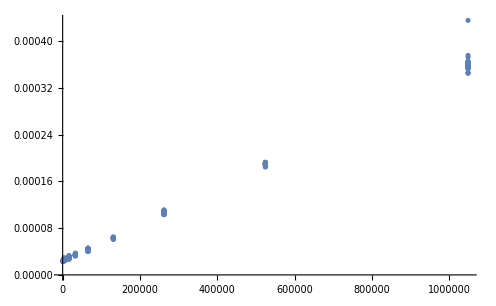

```mathematica
ListPlot[
Lookup[Select[data,#["kind"]==="BatchNormalization"&],{"add_flops","mean_time"}],
PlotRange->All
]
```

```mathematica
Union[Lookup[data,"kind"]]
```

{BatchNormalization,Catenate,Convolution,Elementwise,Pooling,Resize,Total}

## Model Info

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]];
$Models=Keys[SyntheticBenchmark`Assets`Models`$Models];
ClearAll[getModelId];getModelId[name_]:=First[FirstPosition[$Models,name]]
```

```mathematica
files=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data","mxnet_model"}]];
data=Catenate[
Table[
data=Import[file];
header=First[data];
data=AssociationThread[header->#]&/@Rest[data],
{file,files}
]
];
```

```mathematica
Select[data,Last[#]===""&]
```

{<|id→11,name→BPEmb Subword Embeddings Trained on Wikipedia Data,min_time→,mean_time→,max_time→,raw_time→|>,<|id→NotFound,name→Clinical Concept Embeddings Trained on Health Insurance Claims Clinical Narratives from Stanford and PubMed Journal Articles,min_time→,mean_time→,max_time→,raw_time→|>,<|id→17,name→ConceptNet Numberbatch Word Vectors V17.06,min_time→,mean_time→,max_time→,raw_time→|>,<|id→18,name→ConceptNet Numberbatch Word Vectors V17.06 (Raw Model),min_time→,mean_time→,max_time→,raw_time→|>,<|id→34,name→ELMo Contextual Word Representations Trained on 1B Word Benchmark,min_time→,mean_time→,max_time→,raw_time→|>,<|id→NotFound,name→Enhanced Super-Resolution GAN Trained on DIV2K Flickr2K and OST Data,min_time→,mean_time→,max_time→,raw_time→|>,<|id→56,name→Multi-scale Context Aggregation Net Trained on PASCAL VOC2012 Data,min_time→,mean_time→,max_time→,raw_time→|>,<|id→65,name→Self-Normalizing Net for Numeric Data,min_time→,mean_time→,max_time→,raw_time→|>,<|id→66,name→Sentiment Language Model Trained on Amazon Product Review Data,min_time→,mean_time→,max_time→,raw_time→|>,<|id→NotFound,name→SSD-VGG-512 Trained on PASCAL VOC2007 PASCAL VOC2012 and MS-COCO Data,min_time→,mean_time→,max_time→,raw_time→|>}

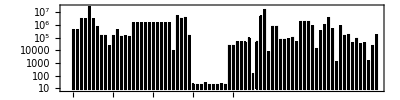

```mathematica
info=Select[data,Last[#]=!=""&];
BarChart[
MapThread[Tooltip,{Lookup[info,"mean_time"],Lookup[info,"name"]}],
ChartLabels->Map[Rotate[Style[getModelId[#] ,FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Lookup[info,"name"]],
BarSpacing->{1,1},
ChartStyle->{Black},
PlotTheme->"Grid",
ScalingFunctions->"Log",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

## Relaxation Rules for Layer Types

```mathematica
files=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data","mxnet_layer_info"}]];
```

```mathematica
data=Import[files[[3]],"CSV"];
header=First[data];
data=AssociationThread[header->#]&/@Rest[data];
```

```mathematica
data[[1]]
```

<|index→26,kind→Catenate,name→inception_3a/output,add_flops→0,div_flops→0,comp_flops→0,exp_flops→0,mad_flops→0,input_channel→64,input_height→28,input_width→28,output_channel→256,output_height→28,output_width→28,function→,kernel_1→,kernel_2→,stride_1→,stride_2→,dilation_1→,dilation_2→,constant_input_overhead→678.,constant_output_overhead→2410.,mad/time→0.,time→98.5|>

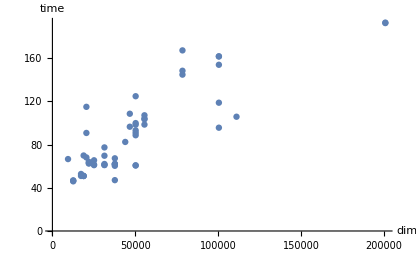

```mathematica
ListPlot[
Transpose[{
Apply[Times,Lookup[data,{"input_channel","input_height","input_width"}],2],
Lookup[data,"time"]
}],
AxesLabel->{"dim","time"}
]
```

## Convolution Modeling2

https://arxiv.org/pdf/1809.07851.pdf

```mathematica
getN[x_,r_,m_]:=Ceiling[(x-r+1)/m]^2
getC[c_]:=c (* input channels *)
getCp[c_] :=c(*output channels *)
```

## Convolution Modeling

```mathematica
convData=Import[FileNameJoin[{NotebookDirectory[],"data","conv_layers","convolution.csv"}]];
header=First[convData];
convData=AssociationThread[header->#]&/@Rest[convData];
```

```mathematica
es=GroupBy[convData,#name&][[1]];
Length[es]
```

25

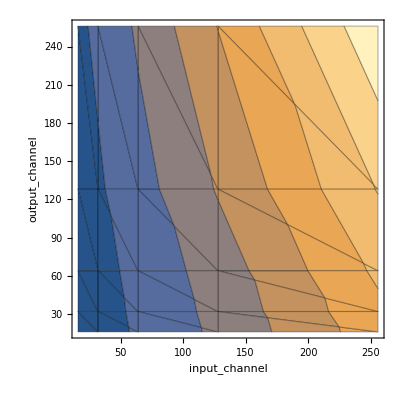

```mathematica
ListContourPlot[
Table[
Transpose[{
Lookup[es,"input_channel"],
Lookup[es,"output_channel"],
Lookup[es,"mean_time"]/1000000
}],
{es,{Values[GroupBy[convData,#name&]][[1]]}}
],
FrameLabel->{"input_channel","output_channel"},
Mesh->All,
PlotRange->All,
InterpolationOrder->1,
PlotLegends->Placed[Automatic,Above],
ImageSize->Scaled[0.5]
]
```

```mathematica
ListPlot3D[
Table[
Transpose[{
Lookup[es,"input_channel"],
Lookup[es,"output_channel"],
Lookup[es,"mean_time"]/1000000
}],
{es,{First@Values[GroupBy[convData,#name&]]}}
],
AxesLabel->{"input_channel","output_channel","mean_time"},
Mesh->All,
PlotRange->All
]
```

-Graphics3D-

```mathematica
ListPlot3D[
Table[
Lookup[es,{"input_channel","output_channel","mean_time"}],
{es,{Values[GroupBy[convData,#name&]][[1]]}}
],
AxesLabel->{"input_channel","output_channel","mean_time"},
Mesh->All,
PlotRange->All
]
```

-Graphics3D-

```mathematica
ps=GroupBy[Values[GroupBy[convData,#name&]][[1]],#["output_channel"]&];
ListLinePlot[
Table[
Callout[Lookup[ps[es],{"input_channel","mean_time"}],es],
{es,Keys[ps]}
],
Mesh->All,
PlotRange->All
]
```

-Graphics-

```mathematica
ps=GroupBy[Values[GroupBy[convData,#name&]][[1]],#["input_channel"]&][[{1,2,3,4}]];
ListLinePlot[
Table[
Callout[Lookup[ps[es],{"output_channel","mean_time"}],es],
{es,Keys[ps]}
],
Mesh->All,
PlotRange->All
]
```

-Graphics-

## Conv InputChannels OutputChannel Relation

```mathematica
es=Import["/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_info/convolution.csv","CSV"];
```

```mathematica
data=AssociationThread[First[es]->#]&/@Rest[es];
```

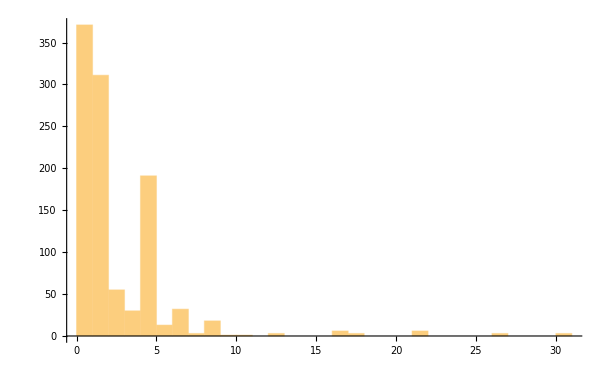

```mathematica
Histogram[Lookup[data,"input_channel"]/Lookup[data,"output_channel"]]
```

```mathematica
es=GroupBy[data,Lookup[#,{"kernel_1","kernel_2","stride_1","stride_2","dilation_1","dilation_2"}]&][[2]]
```

{<|index→5,kind→Convolution,name→2a/res2a_branch1,add_flops→0,div_flops→0,comp_flops→0,exp_flops→0,mad_flops→209715200,9,stride_1→1,stride_2→1,dilation_1→1,dilation_2→1,constant_input_overhead→19824.,constant_output_overhead→40599.,mad/time→5414.24,time→1178.67|>,571}
 |  |  |  |

```mathematica
Keys[es[[1]]]
```

{index,kind,name,add_flops,div_flops,comp_flops,exp_flops,mad_flops,input_channel,input_height,input_width,output_channel,output_height,output_width,function,kernel_1,kernel_2,stride_1,stride_2,dilation_1,dilation_2,constant_input_overhead,constant_output_overhead,mad/time,time}

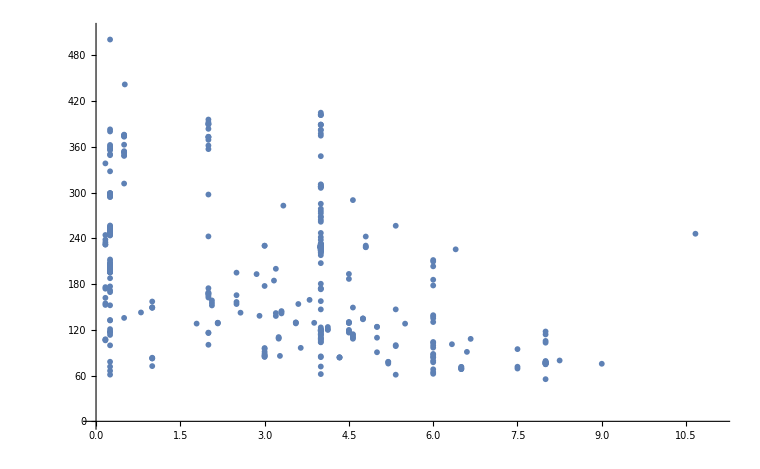

```mathematica
ListPlot[Transpose[{Lookup[es,"input_channel"]/Lookup[es,"output_channel"],Lookup[es,"time"]}]]
```

## Convolution Uniq

```mathematica
convData=Import[FileNameJoin[{NotebookDirectory[],"data","mxnet_layer_info","convolution.csv"}]];
header=First[convData];
convData=AssociationThread[header->#]&/@Rest[convData];
```

```mathematica
Keys[convData[[1]]]
```

{index,kind,name,add_flops,div_flops,comp_flops,exp_flops,mad_flops,input_channel,input_height,input_width,output_channel,output_height,output_width,function,kernel_1,kernel_2,stride_1,stride_2,dilation_1,dilation_2,constant_input_overhead,constant_output_overhead,mad/time,time}

```mathematica
Counts[Lookup[convData,{"output_channel","output_height","output_width"}]]
```

<|{64,320,320}→1,{128,160,160}→7,{256,80,80}→7,{512,40,40}→13,{1024,20,20}→4,{512,20,20}→3,{2048,10,10}→3,{512,10,10}→1,{1024,10,10}→2,{4096,10,10}→2,{64,224,224}→10,{128,112,112}→10,{256,56,56}→37,{512,28,28}→46,{512,14,14}→35,{256,20,20}→1,{256,6,6}→1,{64,112,112}→10,{64,56,56}→31,{192,56,56}→6,{64,28,28}→14,{96,28,28}→6,{128,28,28}→52,{16,28,28}→3,{32,28,28}→11,{192,28,28}→4,{192,14,14}→12,{96,14,14}→9,{208,14,14}→3,{16,14,14}→3,{48,14,14}→5,{64,14,14}→24,{160,14,14}→12,{112,14,14}→6,{224,14,14}→4,{24,14,14}→6,{128,14,14}→37,{256,14,14}→186,{144,14,14}→3,{288,14,14}→4,{32,14,14}→6,{320,14,14}→3,{256,7,7}→10,{160,7,7}→4,{320,7,7}→5,{32,7,7}→3,{128,7,7}→14,{384,7,7}→6,{192,7,7}→7,{48,7,7}→3,{32,149,149}→1,{32,147,147}→1,{64,147,147}→1,{80,73,73}→1,{192,71,71}→1,{64,35,35}→12,{48,35,35}→3,{96,35,35}→7,{32,35,35}→1,{384,17,17}→1,{96,17,17}→1,{192,17,17}→26,{128,17,17}→6,{160,17,17}→12,{320,8,8}→3,{192,8,8}→3,{384,8,8}→12,{448,8,8}→2,{20,24,24}→1,{50,8,8}→1,{48,112,112}→2,{24,112,112}→1,{144,112,112}→1,{144,56,56}→1,{32,56,56}→8,{48,28,28}→3,{288,28,28}→5,{88,14,14}→4,{528,14,14}→8,{136,14,14}→3,{816,14,14}→5,{816,7,7}→1,{224,7,7}→7,{1344,7,7}→6,{448,7,7}→1,{1792,7,7}→1,{1001,1,1}→1,{1024,14,14}→100,{2048,7,7}→20,{512,7,7}→23,{128,56,56}→11,{256,28,28}→13,{64,113,113}→1,{16,56,56}→2,{1000,14,14}→1,{1024,7,7}→9,{64,55,55}→1,{192,55,55}→1,{64,27,27}→9,{96,27,27}→6,{32,27,27}→1,{128,27,27}→1,{352,7,7}→2|>

```mathematica
header
```

{index,kind,name,add_flops,div_flops,comp_flops,exp_flops,mad_flops,input_channel,input_height,input_width,output_channel,output_height,output_width,function,kernel_1,kernel_2,stride_1,stride_2,dilation_1,dilation_2,constant_input_overhead,constant_output_overhead,mad/time,time}

```mathematica
grp=GroupBy[convData,Lookup[#,{"output_channel","output_height","output_width","kernel_1","kernel_2","stride_1","stride_2","dilation_1","dilation_2"}]&];
```

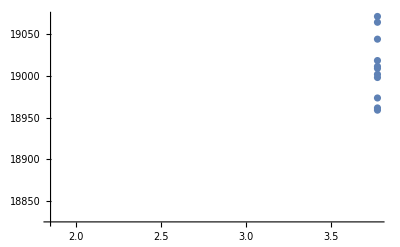
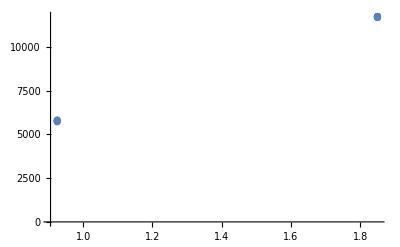
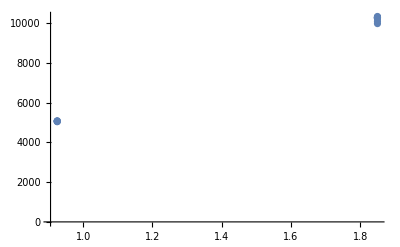
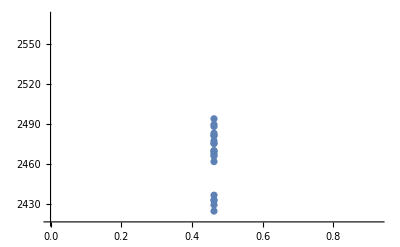
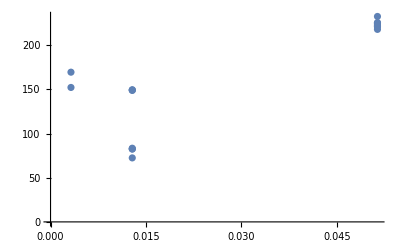
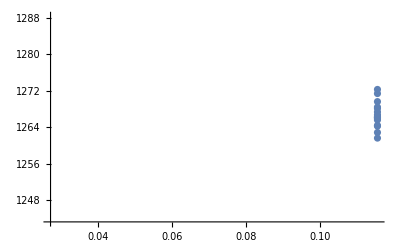
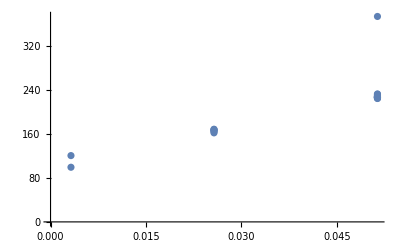
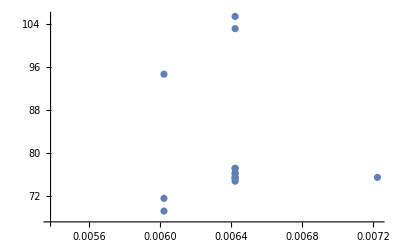
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Grid[Partition[
ListPlot/@Values[Select[
Map[
Transpose[{Lookup[#,"mad_flops"]/10^9,Lookup[#,"time"]}]&,
grp
],
Length[#]>10&
]],UpTo[3]]]
```

```mathematica
Dataset[SelectFirst[grp,Length[#]>6&]]
```

```mathematica
qs=Select[convData,Lookup[#,{"output_channel","output_height","output_width"}]==={256,56,56}&];
AssociationThread[Lookup[qs,"input_channel"]->Lookup[qs,"time"]]
```

<|128→354.433,256→639.533,64→253.3|>

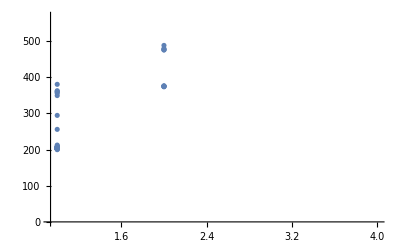

```mathematica
ListPlot[Transpose[{Lookup[qs,"input_channel"]/256,Lookup[qs,"time"]}]]
```

```mathematica
flopMetaTime=AssociationThread[Map[Fold[Times,#]&,Lookup[convData,{"input_channel","output_channel","output_height","output_width"}]]->Lookup[convData,"time"]];
```

```mathematica
features=Normal[flopMetaTime]/.Rule->List;
```

```mathematica
es=DimensionReduce[FeatureExtract[features],2,Method->"TSNE"];
```

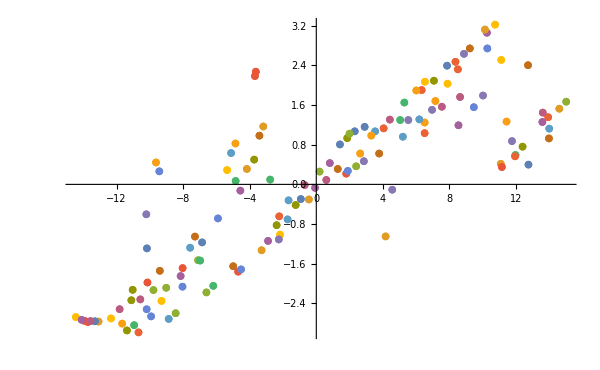

```mathematica
ListPlot[List/@es,ImageSize->600]
```

```mathematica
nlm=NonlinearModelFit[features,Exp[a x/(b+c x)],{a,b,c},x]
```

FittedModel[ⅇ^((3.403 x)/(5.03196×10^6+«1»))]

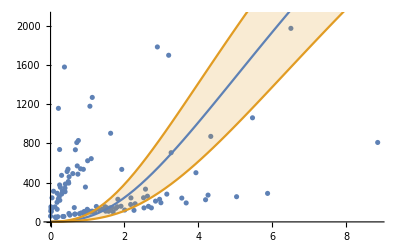

```mathematica
bands90[x_]=nlm["MeanPredictionBands",ConfidenceLevel->.9];
Show[ListPlot[features],Plot[{nlm[x],bands90[x]},{x,1,8*10^7},Filling->{2->{1}}]]
```

## Create MXNet Layer with parameters

```mathematica
models=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data","mxnet_layer_sequence","seq_0"}]];
alldata=(#->Import[#,"CSV"])&/@models;
header=alldata[[1,2,1]];
alldata=Association@Table[model[[1]]->(AssociationThread[header->#]&/@Rest[model[[2]]]),{model,alldata}];
times=Association@KeyValueMap[
Function[{key,val},
info=Import[FileNameJoin[{NotebookDirectory[],"data",FileBaseName[key]<>".csv"}]];
infoHeader=First[info];
info=AssociationThread[infoHeader->#]&/@Rest[info];
info=KeyDrop[info,"time"];
FileBaseName[key]->Table[
infoEntry=SelectFirst[info,#["name"]===layer["sequence_name"]&];
AppendTo[infoEntry,"time"->Lookup[layer,"mean_path_time",0]];
infoEntry,
{layer,val}
]
],
alldata
];
```

split by models and dump

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"data","mxnet_model_info"}];
Quiet[CreateDirectory[baseDir]];
Do[
fileName=FileNameJoin[{baseDir,FileBaseName[t]<>".csv"}];
header=Keys[First[times[t]]];
data=Values/@times[t];
Export[fileName,Join[{header},data],"CSV"]
,
{t,Keys[times]}
];
```

split by layers and dump

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"data","mxnet_layer_info"}];
Quiet[CreateDirectory[baseDir]];
layerInfos=GroupBy[Flatten[Values[times]],#["kind"]&];
Do[
fileName=FileNameJoin[{baseDir,FileBaseName[ToLowerCase[t]]<>".csv"}];
header=Keys[First[layerInfos[t]]];
data=Values/@layerInfos[t];
Export[fileName,Join[{header},data],"CSV"]
,
{t,Keys[layerInfos]}
];
```

## Plot Sequence Time vs Model Time

```mathematica
Exit
```

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
xGet[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]];
$Models=Keys[SyntheticBenchmark`Assets`Models`$Models];
ClearAll[getModelId];getModelId[name_]:=First[FirstPosition[StringReplace[#," "->"_"]&/@$Models,name]]
```

```mathematica
skipModel["LeNet Trained on MNIST Data"|"LeNet_Trained_on_MNIST_Data"]=True;
skipModel[___]:=False
```

```mathematica
timeOfSequence[sequenceLength_]:=
Module[{models,alldata,header},
models=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data","mxnet_layer_sequence","seq_"<>ToString[sequenceLength]}]];
alldata=(#->Import[#,"CSV"])&/@models;
header=alldata[[1,2,1]];
alldata=Association@Table[model[[1]]->(AssociationThread[header->#]&/@Rest[model[[2]]]),{model,alldata}];
Association@KeyValueMap[
Function[{key,val},
FileBaseName[key]->Total[Lookup[val,"mean_path_time",0]]
],
alldata
]
];
networkTime[]:=
Module[{file,data,header},
file=FileNameJoin[{NotebookDirectory[],"data","mxnet_model","mxnet.csv"}];
data=Import[file,{"CSV","Dataset"},"HeaderLines" -> 1];
data=Normal[data[All,{"name","mean_time"}]];
KeySort[Association@Table[elem["name"]->elem["mean_time"],{elem,data}]]
]
```

```mathematica
maxSequence=10;
mxnetTime=networkTime[];
plotData=Association[Table[
sequenceTime=timeOfSequence[sequenceLength];
sequenceLength->Association[Map[
Function[{k},
If[skipModel[k],
Nothing,
k->Tooltip[Lookup[sequenceTime,k,0]/mxnetTime[k],k]
]
],
Keys[mxnetTime]
]],
{sequenceLength,0,maxSequence}
]];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
figs=Association@Table[
sequencePlotData=plotData[sequenceLength];
sequenceLength->BarChart[
sequencePlotData,
ChartLabels->Map[Rotate[Style[getModelId[#] ,FontSize->32,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[sequencePlotData]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->32}
],
{sequenceLength,0,maxSequence}
];
```

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"figs","sequence_length_over_full_time"}];
Quiet[CreateDirectory[baseDir]];
Table[Export[FileNameJoin[{baseDir,StringReplace["seq_" <> ToString[key]," "->"_"]<>".pdf"}], figs[key],ImageSize->Scaled[1.2],ImageResolution->300],{key,Keys[figs]}]
```

{/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_0.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_1.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_2.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_3.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_4.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_5.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_6.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_7.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_8.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_9.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/sequence_length_over_full_time/seq_10.pdf}

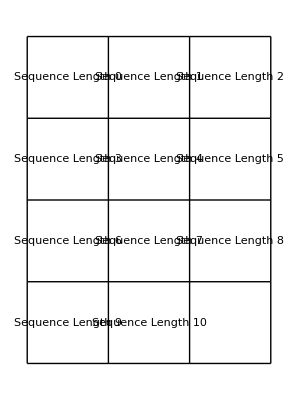

```mathematica
GraphicsGrid[Partition[Table[Labeled[figs[key],"Sequence Length " <> ToString[key]],{key,Keys[figs]}],UpTo[3]],Frame->All,ImageMargins->0, ImageSize->Scaled[1]]
```

## Get Mean Path Time for sequence

```mathematica
sequenceLength=7;
```

```mathematica
models=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data","mxnet_layer_sequence","seq_"<>ToString[sequenceLength]}]];
alldata=(#->Import[#,"CSV"])&/@models;
header=alldata[[1,2,1]];
alldata=Association@Table[model[[1]]->(AssociationThread[header->#]&/@Rest[model[[2]]]),{model,alldata}];
```

```mathematica
Grid[
res=KeyValueMap[
Function[{key,val},
{FileBaseName[key],Total[Lookup[val,"mean_path_time",0]]}
],
alldata
],
Frame->All,
Background->{None,{{White,Lighter[Blend[{Blue,Green}],.9]}}}
]
```

Ademxapp_Model_A_Trained_on_ImageNet_Competition_Data | 735692.
Age_Estimation_VGG-16_Trained_on_IMDB-WIKI_and_Looking_at_People_Data | 153897.
Age_Estimation_VGG-16_Trained_on_IMDB-WIKI_Data | 153711.
CapsNet_Trained_on_MNIST_Data | 132326.
Gender_Prediction_VGG-16_Trained_on_IMDB-WIKI_Data | 154073.
Inception_V1_Trained_on_Extended_Salient_Object_Subitizing_Data | 50069.
Inception_V1_Trained_on_ImageNet_Competition_Data | 47733.6
Inception_V1_Trained_on_Places365_Data | 47186.3
Inception_V3_Trained_on_ImageNet_Competition_Data | 96944.3
LeNet_Trained_on_MNIST_Data | 191.7
MobileNet_V2_Trained_on_ImageNet_Competition_Data | 50964.9
ResNet-101_Trained_on_ImageNet_Competition_Data | 87512.3
ResNet-101_Trained_on_YFCC100m_Geotagged_Data | 80371.7
ResNet-152_Trained_on_ImageNet_Competition_Data | 114620.
ResNet-50_Trained_on_ImageNet_Competition_Data | 45621.4
SqueezeNet_V1.1_Trained_on_ImageNet_Competition_Data | 14831.2
VGG-16_Trained_on_ImageNet_Competition_Data | 154297.
VGG-19_Trained_on_ImageNet_Competition_Data | 180401.
Wide_ResNet-50-2_Trained_on_ImageNet_Competition_Data | 92825.7
Wolfram_ImageIdentify_Net_V1 | 43045.
Yahoo_Open_NSFW_Model_V1 | 27148.

```mathematica
ExportString[res[[All,2]],"CSV"]//CopyToClipboard
```

## Split Into subgraph sequence

```mathematica
sequenceLength=8;
```

```mathematica
models=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"data","mxnet_layer_sequence","seq_"<>ToString[sequenceLength]}]];
alldata=(#->Import[#,"CSV"])&/@models;
header=alldata[[1,2,1]];
alldata=Association@Table[model[[1]]->(AssociationThread[header->#]&/@Rest[model[[2]]]),{model,alldata}];
```

```mathematica
Values[alldata][[1]][[All;;All;;sequenceLength]]//Last
```

<|start_index→129,end_index→137,start_name→7a/res7a_branch2a,end_name→7a/_plus7a,sequence_length→8,sequence_name→7a/res7a_branch2a-7a/bn7a_branch2b1-7a/res7a_branch2b1_relu-7a/res7a_branch2b1-7a/bn7a_branch2b2-7a/res7a_branch2b2_relu-7a/res7a_branch2b2-7a/res7a_branch1-7a/_plus7a,start_layer_kind→Convolution,end_layer_kind→Threading,sequence_layer_kind→Convolution-BatchNormalization-Elementwise-Convolution-BatchNormalization-Elementwise-Convolution-Convolution-Threading,min_start_index_time→824.,mean_start_index_time→834.2,max_start_index_time→1040.,min_end_index_time→225.,mean_end_index_time→226.2,max_end_index_time→344.,min_path_time→,mean_path_time→,max_path_time→,min_path_minus_start_time→,mean_path_minus_start_time→,max_path_minus_start_time→,min_path_minus_end_time→,mean_path_minus_end_time→,max_path_minus_end_time→,raw_start_index_time→{1040., 903., 866., 830., 826., 825., 926., 901., 826., 826., 826., 846., 826., 837., 826., 824., 842., 826., 931., 872., 827., 841., 829., 836., 828., 849., 827., 827., 825., 827., 967., 856., 826., 826., 827., 844., 828., 837., 828., 827., 840., 869., 936., 828., 844., 829., 826., 835., 828., 851.},raw_end_index_time→{344., 303., 233., 227., 226., 227., 226., 226., 225., 232., 226., 237., 228., 226., 226., 225., 226., 226., 226., 226., 226., 227., 226., 226., 226., 225., 227., 225., 226., 236., 226., 226., 226., 226., 226., 226., 226., 226., 225., 226., 225., 225., 226., 225., 227., 225., 239., 229., 228., 227.},raw_path_time→|>

```mathematica
Values[alldata][[1]][[-1]]
```

<|start_index→134,end_index→142,start_name→7a/res7a_branch2b2_relu,end_name→softmax,sequence_length→8,sequence_name→7a/res7a_branch2b2_relu-7a/res7a_branch2b2-7a/res7a_branch1-7a/_plus7a-bn7-relu7-pool7-linear1000-softmax,start_layer_kind→Elementwise,end_layer_kind→Softmax,sequence_layer_kind→Elementwise-Convolution-Convolution-Threading-BatchNormalization-Elementwise-Aggregation-Linear-Softmax,min_start_index_time→100.,mean_start_index_time→101.433,max_start_index_time→149.,min_end_index_time→42.,mean_end_index_time→42.4,max_end_index_time→58.,min_path_time→,mean_path_time→,max_path_time→,min_path_minus_start_time→,mean_path_minus_start_time→,max_path_minus_start_time→,min_path_minus_end_time→,mean_path_minus_end_time→,max_path_minus_end_time→,raw_start_index_time→{149., 121., 104., 103., 103., 101., 102., 101., 102., 101., 102., 102., 102., 101., 102., 101., 101., 101., 101., 102., 101., 112., 102., 101., 102., 102., 101., 100., 102., 101., 101., 101., 101., 102., 102., 101., 101., 101., 101., 101., 102., 101., 101., 102., 101., 101., 102., 101., 101., 102.},raw_end_index_time→{58., 46., 44., 43., 43., 43., 42., 43., 42., 42., 42., 43., 44., 43., 42., 43., 42., 42., 42., 42., 43., 42., 43., 42., 42., 43., 43., 42., 42., 43., 42., 43., 43., 42., 42., 42., 43., 42., 43., 42., 42., 42., 42., 42., 42., 43., 42., 42., 42., 43.},raw_path_time→|>

```mathematica
n=PadRight[Values[alldata][[1]],8*Ceiling[N[Length[Values[alldata][[1]]]/8]],Values[alldata][[1]][[8*Floor[N[Length[Values[alldata][[1]]]/8]]]]]//Length
```

136

```mathematica
processFile[file_]:=
Module[{newFileName,data,len,padElem,clen,flen},
newFileName=StringReplace[file,"mxnet_layer_sequence"->"mxnet_filtered_layer_sequence"];
Quiet[CreateDirectory[DirectoryName[newFileName]]];
data=alldata[file];
len=Length[data];
clen=sequenceLength* Ceiling[len/sequenceLength];
flen=sequenceLength* Floor[len/sequenceLength];
padElem=data[[flen]];
data=PadRight[data,clen,padElem];
data=alldata[file][[All;;All;;sequenceLength+1]];
data
]
```

```mathematica
Lookup[processFile[First[Keys[alldata]]],{"start_index","end_index"}]
```

{{1,9},{10,18},{19,27},{28,36},{37,45},{46,54},{55,63},{64,72},{73,81},{82,90},{91,99},{100,108},{109,117},{118,126},{127,135}}

```mathematica
Do[
,
{file,files}
]
```

{/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Ademxapp_Model_A_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Age_Estimation_VGG-16_Trained_on_IMDB-WIKI_and_Looking_at_People_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Age_Estimation_VGG-16_Trained_on_IMDB-WIKI_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/CapsNet_Trained_on_MNIST_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Gender_Prediction_VGG-16_Trained_on_IMDB-WIKI_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Inception_V1_Trained_on_Extended_Salient_Object_Subitizing_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Inception_V1_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Inception_V1_Trained_on_Places365_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Inception_V3_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/LeNet_Trained_on_MNIST_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/MobileNet_V2_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/ResNet-101_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/ResNet-101_Trained_on_YFCC100m_Geotagged_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/ResNet-152_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/ResNet-50_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/SqueezeNet_V1.1_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/VGG-16_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/VGG-19_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Wide_ResNet-50-2_Trained_on_ImageNet_Competition_Data.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Wolfram_ImageIdentify_Net_V1.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layer_sequence/seq_8/Yahoo_Open_NSFW_Model_V1.csv}

### Change “start_layer_kind” to “end_layer_kind” if you want to split by end layer kind . kind here means conv, concat, etc...

```mathematica
layerPos=First[FirstPosition[header,"start_layer_kind"]];
```

```mathematica
layerData=GroupBy[Select[data,ListQ],#[[layerPos]]&];
baseDir=FileNameJoin[{NotebookDirectory[],"data","mxnet_layers"}];
Quiet[CreateDirectory[baseDir]];
Table[
Export[FileNameJoin[{baseDir,ToLowerCase[layer]<>".csv"}],layerData[layer]],
{layer,Keys[layerData]}
]
```

{/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/convolution.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/pooling.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/batchnormalization.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/elementwise.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/threading.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/aggregation.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/linear.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/flatten.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/dropout.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/transpose.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/reshape.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/replicate.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/constantarray.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/softmax.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/sequencelast.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/ordering.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/extract.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/padding.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/localresponsenormalization.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/catenate.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/part.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/total.csv}

## Split MXNET CSV into layers

```mathematica
files=FileNames["*",FileNameJoin[{NotebookDirectory[],"data","layer_mxnet_sequence"}]];
models=Select[files,!StringStartsQ[FileBaseName[#],"."]&&FileBaseName[#]=!="image_classification"&];
data=Import/@models;
header=data[[1,1]];
data=Flatten[Rest/@data,1];
```

### Change “start_layer_kind” to “end_layer_kind” if you want to split by end layer kind . kind here means conv, concat, etc...

```mathematica
layerPos=First[FirstPosition[header,"start_layer_kind"]];
```

```mathematica
layerData=GroupBy[Select[data,ListQ],#[[layerPos]]&];
baseDir=FileNameJoin[{NotebookDirectory[],"data","mxnet_layers"}];
Quiet[CreateDirectory[baseDir]];
Table[
Export[FileNameJoin[{baseDir,ToLowerCase[layer]<>".csv"}],layerData[layer]],
{layer,Keys[layerData]}
]
```

{/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/convolution.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/pooling.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/batchnormalization.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/elementwise.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/threading.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/aggregation.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/linear.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/flatten.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/dropout.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/transpose.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/reshape.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/replicate.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/constantarray.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/softmax.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/sequencelast.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/ordering.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/extract.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/padding.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/localresponsenormalization.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/catenate.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/part.csv,/Users/abduld/papers/synthetic_benchmark_code/data/mxnet_layers/total.csv}

## Split CSV into layers

```mathematica
files=FileNames["*",FileNameJoin[{NotebookDirectory[],"data"}]];
models=Select[files,!StringStartsQ[FileBaseName[#],"."]&&FileBaseName[#]=!="image_classification"&];
data=Import/@models;
header=data[[1,1]];
data=Flatten[Rest/@data,1];
layerPos=First[FirstPosition[header,"kind"]];
```

```mathematica
layerData=GroupBy[Select[data,ListQ],#[[layerPos]]&];
baseDir=FileNameJoin[{NotebookDirectory[],"data","layers"}];
Quiet[CreateDirectory[baseDir]];
Table[
Export[FileNameJoin[{baseDir,ToLowerCase[layer]<>".csv"}],layerData[layer]],
{layer,Keys[layerData]}
]
```

{/Users/abduld/papers/synthetic_benchmark_code/data/layers/aggregation.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/batchnormalization.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/convolution.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/elementwise.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/linear.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/pooling.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/softmax.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/threading.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/dropout.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/flatten.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/constantarray.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/extract.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/ordering.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/replicate.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/reshape.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/sequencelast.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/transpose.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/catenate.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/localresponsenormalization.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/padding.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/part.csv,/Users/abduld/papers/synthetic_benchmark_code/data/layers/total.csv}

## Flops to Time

```mathematica
modelName="ResNet-50 Trained on ImageNet Competition Data";
```

```mathematica
model=NetModel[modelName];
lyrs=NetInformation[model,"Layers"];
```

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

```mathematica
flopsToCycles[gpu_,net_?NeuralNetworks`ValidNetQ]:=
flopsToCycles[gpu,FlopCount[net]];
flopsToCycles[gpu_,flops_?AssociationQ]:=
Module[{gpuInfo,latencies,mad,add,div,cmp,exp},
gpuInfo=GPUInformation["TESLA V100 SXM2"];
latencies=gpuInfo["InstructionLatency"];
mad=flops["MultiplyAdds"];
add=flops["Additions"];
div=flops["Divisions"];
cmp=flops["Comparisons"];
exp=flops["Exponentiations"];
mad*latencies["fmad"]+add*latencies["fadd"]+div*latencies["fdiv"]+cmp*latencies["and"]+exp*latencies["lg2"]
]
```

```mathematica
flopsToCycles["TESLA V100 SXM2",lyrs[[1]]]
```

472055808

```mathematica
execTimeOf[gpu_,net_?NeuralNetworks`ValidNetQ]:=
execTimeOf[gpu,flopsToCycles[gpu,net]];
execTimeOf[gpu_,flops_?AssociationQ]:=
execTimeOf[gpu,flopsToCycles[gpu,flops]];
execTimeOf[gpu_,cycles_?NumberQ]:=
N[cycles/GPUInformation[gpu]["ClockRate"]];
```

```mathematica
execTimeOf["TESLA V100 SXM2",lyrs[[1]]]
```

308533.

### get time info for all layers on TESLA V100 SXM2

```mathematica
timeInfo=execTimeOf["TESLA V100 SXM2",#]&/@lyrs;
```

```mathematica
header={"layer name","time"};
Grid[
Prepend[MapThread[Prepend,{List/@Values[timeInfo],Keys[timeInfo]}],header],
Frame->All,
Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}
]
```

layer name | time
{conv1} | 308533.
{bn_conv1} | 107567.
{conv1_relu} | 4197.73
{pool1_pad} | 0.
{pool1} | 4722.45
{2a,res2a_branch1} | 134327.
{2a,bn2a_branch1} | 107567.
{2a,res2a_branch2a} | 33581.8
{2a,bn2a_branch2a} | 26891.7
{2a,res2a_branch2a_relu} | 1049.43
{2a,res2a_branch2b} | 302237.
{2a,bn2a_branch2b} | 26891.7
{2a,res2a_branch2b_relu} | 1049.43
{2a,res2a_branch2c} | 134327.
{2a,bn2a_branch2c} | 107567.
{2a,res2a} | 2098.87
{2a,res2a_relu} | 4197.73
{2b,res2b_branch2a} | 134327.
{2b,bn2b_branch2a} | 26891.7
{2b,res2b_branch2a_relu} | 1049.43
{2b,res2b_branch2b} | 302237.
{2b,bn2b_branch2b} | 26891.7
{2b,res2b_branch2b_relu} | 1049.43
{2b,res2b_branch2c} | 134327.
{2b,bn2b_branch2c} | 107567.
{2b,res2b} | 2098.87
{2b,res2b_relu} | 4197.73
{2c,res2c_branch2a} | 134327.
{2c,bn2c_branch2a} | 26891.7
{2c,res2c_branch2a_relu} | 1049.43
{2c,res2c_branch2b} | 302237.
{2c,bn2c_branch2b} | 26891.7
{2c,res2c_branch2b_relu} | 1049.43
{2c,res2c_branch2c} | 134327.
{2c,bn2c_branch2c} | 107567.
{2c,res2c} | 2098.87
{2c,res2c_relu} | 4197.73
{3a,res3a_branch1} | 268655.
{3a,bn3a_branch1} | 53783.4
{3a,res3a_branch2a} | 67163.7
{3a,bn3a_branch2a} | 13445.9
{3a,res3a_branch2a_relu} | 524.716
{3a,res3a_branch2b} | 302237.
{3a,bn3a_branch2b} | 13445.9
{3a,res3a_branch2b_relu} | 524.716
{3a,res3a_branch2c} | 134327.
{3a,bn3a_branch2c} | 53783.4
{3a,res3a} | 1049.43
{3a,res3a_relu} | 2098.87
{3b,res3b_branch2a} | 134327.
{3b,bn3b_branch2a} | 13445.9
{3b,res3b_branch2a_relu} | 524.716
{3b,res3b_branch2b} | 302237.
{3b,bn3b_branch2b} | 13445.9
{3b,res3b_branch2b_relu} | 524.716
{3b,res3b_branch2c} | 134327.
{3b,bn3b_branch2c} | 53783.4
{3b,res3b} | 1049.43
{3b,res3b_relu} | 2098.87
{3c,res3c_branch2a} | 134327.
{3c,bn3c_branch2a} | 13445.9
{3c,res3c_branch2a_relu} | 524.716
{3c,res3c_branch2b} | 302237.
{3c,bn3c_branch2b} | 13445.9
{3c,res3c_branch2b_relu} | 524.716
{3c,res3c_branch2c} | 134327.
{3c,bn3c_branch2c} | 53783.4
{3c,res3c} | 1049.43
{3c,res3c_relu} | 2098.87
{3d,res3d_branch2a} | 134327.
{3d,bn3d_branch2a} | 13445.9
{3d,res3d_branch2a_relu} | 524.716
{3d,res3d_branch2b} | 302237.
{3d,bn3d_branch2b} | 13445.9
{3d,res3d_branch2b_relu} | 524.716
{3d,res3d_branch2c} | 134327.
{3d,bn3d_branch2c} | 53783.4
{3d,res3d} | 1049.43
{3d,res3d_relu} | 2098.87
{4a,res4a_branch1} | 268655.
{4a,bn4a_branch1} | 26891.7
{4a,res4a_branch2a} | 67163.7
{4a,bn4a_branch2a} | 6722.93
{4a,res4a_branch2a_relu} | 262.358
{4a,res4a_branch2b} | 302237.
{4a,bn4a_branch2b} | 6722.93
{4a,res4a_branch2b_relu} | 262.358
{4a,res4a_branch2c} | 134327.
{4a,bn4a_branch2c} | 26891.7
{4a,res4a} | 524.716
{4a,res4a_relu} | 1049.43
{4b,res4b_branch2a} | 134327.
{4b,bn4b_branch2a} | 6722.93
{4b,res4b_branch2a_relu} | 262.358
{4b,res4b_branch2b} | 302237.
{4b,bn4b_branch2b} | 6722.93
{4b,res4b_branch2b_relu} | 262.358
{4b,res4b_branch2c} | 134327.
{4b,bn4b_branch2c} | 26891.7
{4b,res4b} | 524.716
{4b,res4b_relu} | 1049.43
{4c,res4c_branch2a} | 134327.
{4c,bn4c_branch2a} | 6722.93
{4c,res4c_branch2a_relu} | 262.358
{4c,res4c_branch2b} | 302237.
{4c,bn4c_branch2b} | 6722.93
{4c,res4c_branch2b_relu} | 262.358
{4c,res4c_branch2c} | 134327.
{4c,bn4c_branch2c} | 26891.7
{4c,res4c} | 524.716
{4c,res4c_relu} | 1049.43
{4d,res4d_branch2a} | 134327.
{4d,bn4d_branch2a} | 6722.93
{4d,res4d_branch2a_relu} | 262.358
{4d,res4d_branch2b} | 302237.
{4d,bn4d_branch2b} | 6722.93
{4d,res4d_branch2b_relu} | 262.358
{4d,res4d_branch2c} | 134327.
{4d,bn4d_branch2c} | 26891.7
{4d,res4d} | 524.716
{4d,res4d_relu} | 1049.43
{4e,res4e_branch2a} | 134327.
{4e,bn4e_branch2a} | 6722.93
{4e,res4e_branch2a_relu} | 262.358
{4e,res4e_branch2b} | 302237.
{4e,bn4e_branch2b} | 6722.93
{4e,res4e_branch2b_relu} | 262.358
{4e,res4e_branch2c} | 134327.
{4e,bn4e_branch2c} | 26891.7
{4e,res4e} | 524.716
{4e,res4e_relu} | 1049.43
{4f,res4f_branch2a} | 134327.
{4f,bn4f_branch2a} | 6722.93
{4f,res4f_branch2a_relu} | 262.358
{4f,res4f_branch2b} | 302237.
{4f,bn4f_branch2b} | 6722.93
{4f,res4f_branch2b_relu} | 262.358
{4f,res4f_branch2c} | 134327.
{4f,bn4f_branch2c} | 26891.7
{4f,res4f} | 524.716
{4f,res4f_relu} | 1049.43
{5a,res5a_branch1} | 268655.
{5a,bn5a_branch1} | 13445.9
{5a,res5a_branch2a} | 67163.7
{5a,bn5a_branch2a} | 3361.46
{5a,res5a_branch2a_relu} | 131.179
{5a,res5a_branch2b} | 302237.
{5a,bn5a_branch2b} | 3361.46
{5a,res5a_branch2b_relu} | 131.179
{5a,res5a_branch2c} | 134327.
{5a,bn5a_branch2c} | 13445.9
{5a,res5a} | 262.358
{5a,res5a_relu} | 524.716
{5b,res5b_branch2a} | 134327.
{5b,bn5b_branch2a} | 3361.46
{5b,res5b_branch2a_relu} | 131.179
{5b,res5b_branch2b} | 302237.
{5b,bn5b_branch2b} | 3361.46
{5b,res5b_branch2b_relu} | 131.179
{5b,res5b_branch2c} | 134327.
{5b,bn5b_branch2c} | 13445.9
{5b,res5b} | 262.358
{5b,res5b_relu} | 524.716
{5c,res5c_branch2a} | 134327.
{5c,bn5c_branch2a} | 3361.46
{5c,res5c_branch2a_relu} | 131.179
{5c,res5c_branch2b} | 302237.
{5c,bn5c_branch2b} | 3361.46
{5c,res5c_branch2b_relu} | 131.179
{5c,res5c_branch2c} | 134327.
{5c,bn5c_branch2c} | 13445.9
{5c,res5c} | 262.358
{5c,res5c_relu} | 524.716
{pool5} | 262.358
{flatten_0} | 0.
{fc1000} | 5354.25
{prob} | 154.248

### find Nearest for time on TESLA V100 SXM2

```mathematica
timeInfo=execTimeOf["TESLA V100 SXM2",#]&/@lyrs;
```

```mathematica
nf=Nearest[Values[timeInfo]->Keys[lyrs]]
```

NearestFunction[…]

```mathematica
lyrOfInterest=lyrs[[2]]
```

BatchNormalizationLayer[<>]

```mathematica
nearestLayers=nf[execTimeOf["TESLA V100 SXM2",lyrOfInterest]]
```

{{bn_conv1},{2a,bn2a_branch1},{2a,bn2a_branch2c},{2b,bn2b_branch2c},{2c,bn2c_branch2c}}

```mathematica
Lookup[lyrs,nearestLayers]
```

{BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>]}

## GPU Information

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

```mathematica
GPUMemoryLatency["Volta"]
```

<|l1_cache_access→26,l2_cache_access→198,global_mem_latency→362,local_mem_latency→362,constant_mem_latency→8,texture_mem_latency→436,texture_cache_latency→86,shared_mem_latency→18|>

```mathematica
GPUInstructionLatency["Volta"]
```

<|add→4,sub→4,min→4,max→4,mul→4,mad→4,sdiv→127,srem→125,abs→8,udiv→122,urem→117,and→4,or→4,not→4,xor→4,cnot→8,shl→4,shr→4,fadd→4,fsub→4,fmul→4,fmad→4,fma→4,fdiv→201,dadd→8,dsub→8,dmin→8,dmax→8,dmul→8,dmad→8,dfma→8,ddiv→159,hfadd→6,hfsub→6,hfmul→6,hffma→6,add.cc→4,addc→4,sub.cc→4,subc→8,mad.cc→4,madc→4,rcp→60,sqrt→60,fasqrt→31,rsqrt→31,sin→11,cos→11,lg2→31,ex2→22,copysign→8,mul24→12,mad24→12,mulhi→12,dmulhi→123,sad→4,popc→15,clz→5,bfe→4,bfi→4,bfind→15,bbrev→15,mov→4,shfl→4,cvta→4,cvt→4,selp→4,setp→4|>

```mathematica
GPUInformation["TESLA V100 SXM2"]
```

<|Name→TESLA V100 SXM2,Architecture→Volta,InstructionLatency→<|add→4,sub→4,min→4,max→4,mul→4,mad→4,sdiv→127,srem→125,abs→8,udiv→122,urem→117,and→4,or→4,not→4,xor→4,cnot→8,shl→4,shr→4,fadd→4,fsub→4,fmul→4,fmad→4,fma→4,fdiv→201,dadd→8,dsub→8,dmin→8,dmax→8,dmul→8,dmad→8,dfma→8,ddiv→159,hfadd→6,hfsub→6,hfmul→6,hffma→6,add.cc→4,addc→4,sub.cc→4,subc→8,mad.cc→4,madc→4,rcp→60,sqrt→60,fasqrt→31,rsqrt→31,sin→11,cos→11,lg2→31,ex2→22,copysign→8,mul24→12,mad24→12,mulhi→12,dmulhi→123,sad→4,popc→15,clz→5,bfe→4,bfi→4,bfind→15,bbrev→15,mov→4,shfl→4,cvta→4,cvt→4,selp→4,setp→4|>,MemoryLatency→<|l1_cache_access→26,l2_cache_access→198,global_mem_latency→362,local_mem_latency→362,constant_mem_latency→8,texture_mem_latency→436,texture_cache_latency→86,shared_mem_latency→18|>,Interconnect→<|Name→SXM2,Bandwidth→Missing[SXM2,Not implemented]|>,ClockRate→1530,PeekGFlops→15000,MemoryBandwidth→900|>

## Flop Count

```mathematica
modelName="ResNet-50 Trained on ImageNet Competition Data";
```

```mathematica
model=NetModel[modelName];
lyrs=NetInformation[model,"Layers"];
```

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

### get flop info for all layers

```mathematica
flopsInfo=FlopCount/@lyrs;
```

```mathematica
header=Prepend[Keys[flopsInfo[[1]]],"layer name"];
Grid[
Prepend[MapThread[Prepend,{Values/@Values[flopsInfo],Keys[flopsInfo]}],header],
Frame->All,
Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}
]
```

layer name | MultiplyAdds | Additions | Divisions | Comparisons | Exponentiations
{conv1} | 118013952 | 0 | 0 | 0 | 0
{bn_conv1} | 0 | 802816 | 802816 | 0 | 0
{conv1_relu} | 802816 | 0 | 0 | 802816 | 0
{pool1_pad} | 0 | 0 | 0 | 0 | 0
{pool1} | 0 | 0 | 0 | 1806336 | 0
{2a,res2a_branch1} | 51380224 | 0 | 0 | 0 | 0
{2a,bn2a_branch1} | 0 | 802816 | 802816 | 0 | 0
{2a,res2a_branch2a} | 12845056 | 0 | 0 | 0 | 0
{2a,bn2a_branch2a} | 0 | 200704 | 200704 | 0 | 0
{2a,res2a_branch2a_relu} | 200704 | 0 | 0 | 200704 | 0
{2a,res2a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{2a,bn2a_branch2b} | 0 | 200704 | 200704 | 0 | 0
{2a,res2a_branch2b_relu} | 200704 | 0 | 0 | 200704 | 0
{2a,res2a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{2a,bn2a_branch2c} | 0 | 802816 | 802816 | 0 | 0
{2a,res2a} | 0 | 802816 | 0 | 0 | 0
{2a,res2a_relu} | 802816 | 0 | 0 | 802816 | 0
{2b,res2b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{2b,bn2b_branch2a} | 0 | 200704 | 200704 | 0 | 0
{2b,res2b_branch2a_relu} | 200704 | 0 | 0 | 200704 | 0
{2b,res2b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{2b,bn2b_branch2b} | 0 | 200704 | 200704 | 0 | 0
{2b,res2b_branch2b_relu} | 200704 | 0 | 0 | 200704 | 0
{2b,res2b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{2b,bn2b_branch2c} | 0 | 802816 | 802816 | 0 | 0
{2b,res2b} | 0 | 802816 | 0 | 0 | 0
{2b,res2b_relu} | 802816 | 0 | 0 | 802816 | 0
{2c,res2c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{2c,bn2c_branch2a} | 0 | 200704 | 200704 | 0 | 0
{2c,res2c_branch2a_relu} | 200704 | 0 | 0 | 200704 | 0
{2c,res2c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{2c,bn2c_branch2b} | 0 | 200704 | 200704 | 0 | 0
{2c,res2c_branch2b_relu} | 200704 | 0 | 0 | 200704 | 0
{2c,res2c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{2c,bn2c_branch2c} | 0 | 802816 | 802816 | 0 | 0
{2c,res2c} | 0 | 802816 | 0 | 0 | 0
{2c,res2c_relu} | 802816 | 0 | 0 | 802816 | 0
{3a,res3a_branch1} | 102760448 | 0 | 0 | 0 | 0
{3a,bn3a_branch1} | 0 | 401408 | 401408 | 0 | 0
{3a,res3a_branch2a} | 25690112 | 0 | 0 | 0 | 0
{3a,bn3a_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3a,res3a_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3a,res3a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3a,bn3a_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3a,res3a_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3a,res3a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3a,bn3a_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3a,res3a} | 0 | 401408 | 0 | 0 | 0
{3a,res3a_relu} | 401408 | 0 | 0 | 401408 | 0
{3b,res3b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{3b,bn3b_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3b,res3b_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3b,res3b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3b,bn3b_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3b,res3b_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3b,res3b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3b,bn3b_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3b,res3b} | 0 | 401408 | 0 | 0 | 0
{3b,res3b_relu} | 401408 | 0 | 0 | 401408 | 0
{3c,res3c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{3c,bn3c_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3c,res3c_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3c,res3c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3c,bn3c_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3c,res3c_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3c,res3c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3c,bn3c_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3c,res3c} | 0 | 401408 | 0 | 0 | 0
{3c,res3c_relu} | 401408 | 0 | 0 | 401408 | 0
{3d,res3d_branch2a} | 51380224 | 0 | 0 | 0 | 0
{3d,bn3d_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3d,res3d_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3d,res3d_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3d,bn3d_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3d,res3d_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3d,res3d_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3d,bn3d_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3d,res3d} | 0 | 401408 | 0 | 0 | 0
{3d,res3d_relu} | 401408 | 0 | 0 | 401408 | 0
{4a,res4a_branch1} | 102760448 | 0 | 0 | 0 | 0
{4a,bn4a_branch1} | 0 | 200704 | 200704 | 0 | 0
{4a,res4a_branch2a} | 25690112 | 0 | 0 | 0 | 0
{4a,bn4a_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4a,res4a_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4a,res4a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4a,bn4a_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4a,res4a_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4a,res4a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4a,bn4a_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4a,res4a} | 0 | 200704 | 0 | 0 | 0
{4a,res4a_relu} | 200704 | 0 | 0 | 200704 | 0
{4b,res4b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4b,bn4b_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4b,res4b_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4b,res4b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4b,bn4b_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4b,res4b_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4b,res4b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4b,bn4b_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4b,res4b} | 0 | 200704 | 0 | 0 | 0
{4b,res4b_relu} | 200704 | 0 | 0 | 200704 | 0
{4c,res4c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4c,bn4c_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4c,res4c_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4c,res4c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4c,bn4c_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4c,res4c_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4c,res4c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4c,bn4c_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4c,res4c} | 0 | 200704 | 0 | 0 | 0
{4c,res4c_relu} | 200704 | 0 | 0 | 200704 | 0
{4d,res4d_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4d,bn4d_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4d,res4d_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4d,res4d_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4d,bn4d_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4d,res4d_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4d,res4d_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4d,bn4d_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4d,res4d} | 0 | 200704 | 0 | 0 | 0
{4d,res4d_relu} | 200704 | 0 | 0 | 200704 | 0
{4e,res4e_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4e,bn4e_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4e,res4e_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4e,res4e_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4e,bn4e_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4e,res4e_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4e,res4e_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4e,bn4e_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4e,res4e} | 0 | 200704 | 0 | 0 | 0
{4e,res4e_relu} | 200704 | 0 | 0 | 200704 | 0
{4f,res4f_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4f,bn4f_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4f,res4f_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4f,res4f_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4f,bn4f_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4f,res4f_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4f,res4f_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4f,bn4f_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4f,res4f} | 0 | 200704 | 0 | 0 | 0
{4f,res4f_relu} | 200704 | 0 | 0 | 200704 | 0
{5a,res5a_branch1} | 102760448 | 0 | 0 | 0 | 0
{5a,bn5a_branch1} | 0 | 100352 | 100352 | 0 | 0
{5a,res5a_branch2a} | 25690112 | 0 | 0 | 0 | 0
{5a,bn5a_branch2a} | 0 | 25088 | 25088 | 0 | 0
{5a,res5a_branch2a_relu} | 25088 | 0 | 0 | 25088 | 0
{5a,res5a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{5a,bn5a_branch2b} | 0 | 25088 | 25088 | 0 | 0
{5a,res5a_branch2b_relu} | 25088 | 0 | 0 | 25088 | 0
{5a,res5a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{5a,bn5a_branch2c} | 0 | 100352 | 100352 | 0 | 0
{5a,res5a} | 0 | 100352 | 0 | 0 | 0
{5a,res5a_relu} | 100352 | 0 | 0 | 100352 | 0
{5b,res5b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{5b,bn5b_branch2a} | 0 | 25088 | 25088 | 0 | 0
{5b,res5b_branch2a_relu} | 25088 | 0 | 0 | 25088 | 0
{5b,res5b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{5b,bn5b_branch2b} | 0 | 25088 | 25088 | 0 | 0
{5b,res5b_branch2b_relu} | 25088 | 0 | 0 | 25088 | 0
{5b,res5b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{5b,bn5b_branch2c} | 0 | 100352 | 100352 | 0 | 0
{5b,res5b} | 0 | 100352 | 0 | 0 | 0
{5b,res5b_relu} | 100352 | 0 | 0 | 100352 | 0
{5c,res5c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{5c,bn5c_branch2a} | 0 | 25088 | 25088 | 0 | 0
{5c,res5c_branch2a_relu} | 25088 | 0 | 0 | 25088 | 0
{5c,res5c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{5c,bn5c_branch2b} | 0 | 25088 | 25088 | 0 | 0
{5c,res5c_branch2b_relu} | 25088 | 0 | 0 | 25088 | 0
{5c,res5c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{5c,bn5c_branch2c} | 0 | 100352 | 100352 | 0 | 0
{5c,res5c} | 0 | 100352 | 0 | 0 | 0
{5c,res5c_relu} | 100352 | 0 | 0 | 100352 | 0
{pool5} | 0 | 100352 | 0 | 0 | 0
{flatten_0} | 0 | 0 | 0 | 0 | 0
{fc1000} | 2048000 | 0 | 0 | 0 | 0
{prob} | 0 | 1000 | 1000 | 0 | 1000

### find Nearest for flops

```mathematica
flopsInfo=FlopCount/@lyrs;
```

```mathematica
nf=Nearest[(Values/@Values[flopsInfo])->Keys[lyrs]]
```

NearestFunction[…]

```mathematica
lyrOfInterest=lyrs[[2]]
```

BatchNormalizationLayer[<>]

```mathematica
nearestLayers=nf[Values[FlopCount[lyrOfInterest]]]
```

{{bn_conv1},{2a,bn2a_branch1},{2a,bn2a_branch2c},{2b,bn2b_branch2c},{2c,bn2c_branch2c}}

```mathematica
Lookup[lyrs,nearestLayers]
```

{BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>]}

### All Models

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

```mathematica
modelTask=GroupBy[Table[model->If[NetModel[ model,"TaskType"]==={},"Other",First[NetModel[ model,"TaskType"]]],{model,Keys[$Models]}]];models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
taskName="Classification";
```

```mathematica
lyrs=Union[Flatten[Lookup[$Models,models[taskName]]]];
```

```mathematica
<<SyntheticBenchmark`StaticAnalysis`
es=RandomSample[lyrs];
Select[Check[FlopCount[#],Throw[#]]&/@es,!AssociationQ[#]&]
```

{}

```mathematica
<<SyntheticBenchmark`StaticAnalysis`
AssociationThread[es->(FlopCount/@es)][[;;10]]
```

<|LinearLayer[<|Type→Linear,Arrays→Null,Parameters→<|OutputDimensions→{4096},$OutputSize→4096,$InputSize→25088,$InputDimensions→{25088}|>,Inputs→<|Input→TensorT[{25088},RealT]|>,Outputs→<|Output→TensorT[{4096},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→102760448,Additions→0,Divisions→0,Comparisons→0,Exponentiations→0|>,ElementwiseLayer[<|Type→Elementwise,Arrays→Null,Parameters→<|Function→ValidatedParameter[Ramp],$Dimensions→{32,14,14}|>,Inputs→<|Input→TensorT[{32,14,14},RealT]|>,Outputs→<|Output→TensorT[{32,14,14},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→6272,Additions→0,Divisions→0,Comparisons→6272,Exponentiations→0|>,ElementwiseLayer[<|Type→Elementwise,Arrays→Null,Parameters→<|Function→ValidatedParameter[Ramp],$Dimensions→{384,17,17}|>,Inputs→<|Input→TensorT[{384,17,17},RealT]|>,Outputs→<|Output→TensorT[{384,17,17},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→110976,Additions→0,Divisions→0,Comparisons→110976,Exponentiations→0|>,LinearLayer[<|Type→Linear,Arrays→Null,Parameters→<|OutputDimensions→{512},$OutputSize→512,$InputSize→16,$InputDimensions→{16}|>,Inputs→<|Input→TensorT[{16},RealT]|>,Outputs→<|Output→TensorT[{512},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→8192,Additions→0,Divisions→0,Comparisons→0,Exponentiations→0|>,ElementwiseLayer[<|Type→Elementwise,Arrays→Null,Parameters→<|Function→ValidatedParameter[Ramp],$Dimensions→{256,14,14}|>,Inputs→<|Input→TensorT[{256,14,14},RealT]|>,Outputs→<|Output→TensorT[{256,14,14},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→50176,Additions→0,Divisions→0,Comparisons→50176,Exponentiations→0|>,BatchNormalizationLayer[<|Type→BatchNormalization,Arrays→Null,Parameters→<|Momentum→0.9,Epsilon→0.0000100001,$Channels→224,Interleaving→False,$SpatialDimensions→{14,14}|>,Inputs→<|Input→TensorT[{224,14,14},RealT]|>,Outputs→<|Output→TensorT[{224,14,14},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→0,Additions→43904,Divisions→43904,Comparisons→0,Exponentiations→0|>,ConvolutionLayer[<|Type→Convolution,Arrays→Null,Parameters→<|OutputChannels→192,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,$InputChannels→64,ChannelGroups→1,$InputSize→{56,56},$OutputSize→{56,56},Interleaving→False,$WeightsInputChannels→64|>,Inputs→<|Input→TensorT[{64,56,56},RealT]|>,Outputs→<|Output→TensorT[{192,56,56},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→346816512,Additions→0,Divisions→0,Comparisons→0,Exponentiations→0|>,BatchNormalizationLayer[<|Type→BatchNormalization,Arrays→Null,Parameters→<|Momentum→0.9,Epsilon→0.0001,$Channels→128,Interleaving→False,$SpatialDimensions→{14,14}|>,Inputs→<|Input→TensorT[{128,14,14},RealT]|>,Outputs→<|Output→TensorT[{128,14,14},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→0,Additions→25088,Divisions→25088,Comparisons→0,Exponentiations→0|>,BatchNormalizationLayer[<|Type→BatchNormalization,Arrays→Null,Parameters→<|Momentum→0.9,Epsilon→0.001,Interleaving→False,$Channels→288,$SpatialDimensions→{28,28}|>,Inputs→<|Input→TensorT[{288,28,28},RealT]|>,Outputs→<|Output→TensorT[{288,28,28},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→0,Additions→225792,Divisions→225792,Comparisons→0,Exponentiations→0|>,ConvolutionLayer[<|Type→Convolution,Arrays→Null,Parameters→<|OutputChannels→96,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,$InputChannels→96,ChannelGroups→1,$InputSize→{27,27},$OutputSize→{27,27},Interleaving→False,$WeightsInputChannels→96|>,Inputs→<|Input→TensorT[{96,27,27},RealT]|>,Outputs→<|Output→TensorT[{96,27,27},RealT]|>|>,<|Version→12.0.12,Unstable→False|>]→<|MultiplyAdds→60466176,Additions→0,Divisions→0,Comparisons→0,Exponentiations→0|>|>

## Layer Patterns

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
layerNameKinds=Flatten[Table[
model=NetModel[modelName];
gr=NetInformation[model,"LayersGraph"];
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
layers=SymbolName/@layers[[All,0]];
Append[layers,"NONE"],
{modelName,$ModelNames}
]];
```

```mathematica
shortenName[s_String]:=StringReplace[s,{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}];
shortenName[s_?Developer`SymbolQ]:=shortenName[SymbolName[s]]
```

```mathematica
mkChart[n_]:=Module[{tuples,stuples},
tuples=Association[Counts[Partition[layerNameKinds,n,1]]];
stuples=Take[ReverseSort[KeyMap[StringRiffle[Map[shortenName,#],"⟩"]&,tuples]],UpTo[10]];
BarChart[
stuples,
ChartLabels->Map[Rotate[Style[#,FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[stuples]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
]
```

### Size 2 patterns

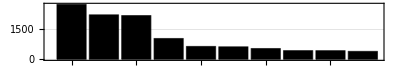

```mathematica
mkChart[2]
```

### Size 3 patterns

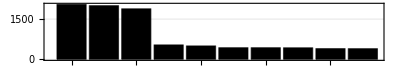

```mathematica
mkChart[3]
```

### Size 4 patterns

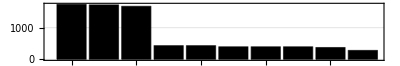

```mathematica
mkChart[4]
```

### Size 5 patterns

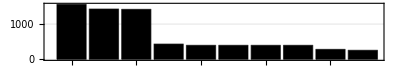

```mathematica
mkChart[5]
```

### Size 6 patterns

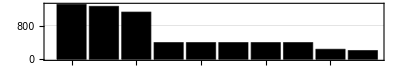

```mathematica
mkChart[6]
```

## NetInformation Metadata

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
$ModelNames[[20]]
```

CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data

```mathematica
model=NetModel[$ModelNames[[20]]];
```

```mathematica
NetInformation[model,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

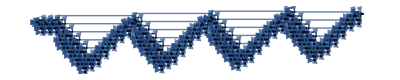

```mathematica
gr=NetInformation[model,"LayersGraph"]
```

### Mc

https://blog.wolfram.com/2013/02/04/centennial-of-markov-chains/

```mathematica
Frequencies[data_]:=Block[{ta=Tally[data]},ta[[All,2]]/=N[Length[data]];Rule@@@ta]
```

```mathematica
gr=NetInformation[model,"LayersGraph"];
verts=VertexList[gr];
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
```

```mathematica
layerNameKinds=Flatten[Parallelize@Table[
model=NetModel[modelName];
gr=NetInformation[model,"LayersGraph"];
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
layers=SymbolName/@layers[[All,0]];
Append[layers,"NONE"],
{modelName,$ModelNames}
]];
fverts=Frequencies[layerNameKinds];
fvertTup=Frequencies[Partition[layerNameKinds,2,1]];
```

```mathematica
Length[layerNameKinds]
```

91

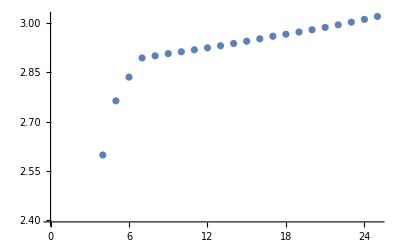

```mathematica
Table[{k,Entropy[Partition[layerNameKinds,k,1]]//N},{k,1,25}]//ListPlot
```

```mathematica
condprobs=Catenate@Table[
Frequencies[Cases[Partition[layerNameKinds,2,1],{lyr,_}]],{lyr,layerNameKinds}];
```

```mathematica
MatrixForm[tm=Outer[List,Union[layerNameKinds],Union[layerNameKinds]]/.Append[condprobs,{_,_}->0]]
```

(0 | 0 | 0.0454545 | 0.954545 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0
0.133333 | 0.0666667 | 0 | 0 | 0.8 | 0 | 0
0 | 0 | 0.608696 | 0 | 0 | 0 | 0.391304
1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0.111111 | 0 | 0 | 0.888889 | 0 | 0)

```mathematica
mproc=DiscreteMarkovProcess[1,tm]
```

DiscreteMarkovProcess[1,{{0,0,0.0454545,0.954545,0,0,0},{0,0,0,0,0,1.,0},{0.133333,0.0666667,0,0,0.8,0,0},{0,0,0.608696,0,0,0,0.391304},{1.,0,0,0,0,0,0},{0,0,0,1.,0,0,0},{0,0.111111,0,0,0.888889,0,0}}]

```mathematica
Mean[FirstPassageTimeDistribution[mproc,1]]
```

4.22727

```mathematica
DiscretePlot[PDF[FirstPassageTimeDistribution[mproc,1],n],{n,1,10},ExtentSize->{0,2/3},PlotStyle->Black]
```

-Graphics-

```mathematica
(gram4data=Flatten[Frequencies/@GatherBy[Partition[layerNameKinds,4,1],Most]]//N)//Short[#,3]&
```

{{ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer}→0.916667,«18»,{ElementwiseLayer,DeconvolutionLayer,PartLayer,NormalizationLayer}→1.}

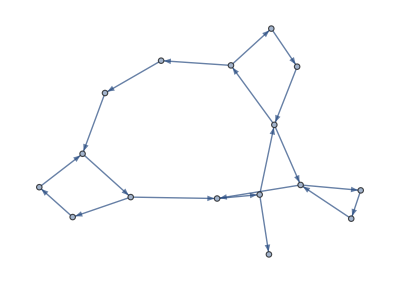

```mathematica
gram4gr=Graph[gram4data/.{HoldPattern[{w1_,w2_,w3_,w4_}->p_]:>Property[{w1,w2,w3}->{w2,w3,w4},"Probability"->p]},PerformanceGoal->"Speed"]
```

```mathematica
initialProbabilityVector=SparseArray[VertexList[gram4gr]/.Frequencies[Partition[layerNameKinds,3,1]]];
```

```mathematica
transitionMat=WeightedAdjacencyMatrix[gram4gr,EdgeWeight->"Probability"]
```

SparseArray[…]

```mathematica
mc=DiscreteMarkovProcess[initialProbabilityVector//N,transitionMat]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

DiscreteMarkovProcess[{0.130435,0.206522,0.0108696,0.130435,0.0978261,0.0217391,0.119565,0.0217391,0.0869565,0.0108696,0.0869565,0.0108696,0.0217391,0.0217391,0.0108696,0.0108696},{{0.,0.916667,0.0833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.526316,0.473684,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.166667,0.833333,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.888889,0.111111,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.}}]

```mathematica
GramListToText[list_]:=StringJoin[Riffle[Join[First[list],Rest[list][[All,-1]]]," "]]
```

```mathematica
GramListToText[Extract[VertexList[gram4gr],Transpose[RandomFunction[mc,{0,100}]["States"]]]]
```

ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer

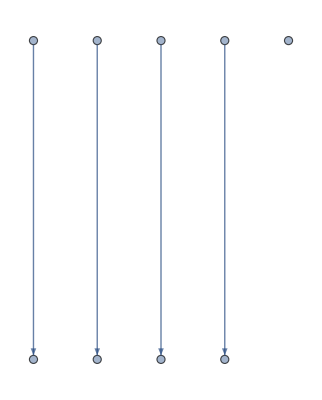

```mathematica
lines=VertexDelete[gram4gr,VertexList[gram4gr, x_/;VertexDegree[gram4gr,x]>2]]
```

```mathematica
lineData=WeaklyConnectedComponents[lines];
```

### topological order

```mathematica
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
layerNameKinds=layers[[All,0]]
```

{ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,DeconvolutionLayer,PartLayer,NormalizationLayer,ElementwiseLayer,DeconvolutionLayer,PartLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,ElementwiseLayer}

```mathematica
verts=VertexList[gr];
edges=EdgeList[gr];
```

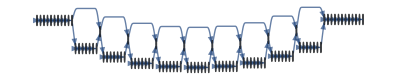

```mathematica
gre=Graph[verts,edges,Options[gr],AnnotationRules->Join[
Table[vert->{"InitialProbability"->1/Length[verts]},{vert,verts}],
Table[edge->{"Probability"->1},{edge,edges}]
]]
```

```mathematica
de=DiscreteMarkovProcess[gre];
```

```mathematica
tmp=RandomFunction[de,{0,10}]
```

TemporalData[…]

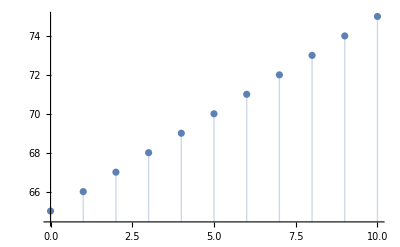

```mathematica
ListPlot[tmp,Filling->Axis]
```

```mathematica
sim=RandomFunction[de,{0,10},4*10,Method->{Automatic,"StoppingFunction"->Function[{len,pos},len<10&&pos≠1||len==1]}]
```

TemporalData[…]

```mathematica
Normal[sim]
```

{{{0,72},{1,73},{2,74},{3,75},{4,76},{5,77},{6,78},{7,79},{8,80},{9,81}},{{0,66},{1,67},{2,68},{3,69},{4,70},{5,71},{6,72},{7,73},{8,74},{9,75}},{{0,15},{1,16},{2,17},{3,18},{4,19},{5,20},{6,21},{7,22},{8,23},{9,24}},{{0,81},{1,82},{2,83},{3,84},{4,85},{5,86},{6,87},{7,88},{8,89},{9,90}},{{0,51},{1,52},{2,53},{3,54},{4,55},{5,56},{6,57},{7,58},{8,59},{9,67}},{{0,51},{1,59},{2,67},{3,68},{4,69},{5,70},{6,71},{7,72},{8,73},{9,74}},{{0,35},{1,43},{2,51},{3,52},{4,53},{5,54},{6,55},{7,56},{8,57},{9,58}},{{0,3},{1,4},{2,5},{3,6},{4,7},{5,8},{6,9},{7,10},{8,11},{9,12}},{{0,66},{1,67},{2,75},{3,83},{4,84},{5,85},{6,86},{7,87},{8,88},{9,89}},{{0,79},{1,80},{2,81},{3,82},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,70},{1,71},{2,72},{3,73},{4,74},{5,75},{6,76},{7,77},{8,78},{9,79}},{{0,41},{1,42},{2,43},{3,44},{4,45},{5,46},{6,47},{7,48},{8,49},{9,50}},{{0,18},{1,19},{2,27},{3,28},{4,29},{5,30},{6,31},{7,32},{8,33},{9,34}},{{0,58},{1,59},{2,67},{3,75},{4,76},{5,77},{6,78},{7,79},{8,80},{9,81}},{{0,78},{1,79},{2,80},{3,81},{4,82},{5,83},{6,84},{7,85},{8,86},{9,87}},{{0,79},{1,80},{2,81},{3,82},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,75},{1,83},{2,84},{3,85},{4,86},{5,87},{6,88},{7,89},{8,90},{9,91}},{{0,5},{1,6},{2,7},{3,8},{4,9},{5,10},{6,11},{7,12},{8,13},{9,14}},{{0,53},{1,54},{2,55},{3,56},{4,57},{5,58},{6,59},{7,67},{8,75},{9,83}},{{0,58},{1,59},{2,67},{3,75},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,37},{1,38},{2,39},{3,40},{4,41},{5,42},{6,43},{7,44},{8,45},{9,46}},{{0,86},{1,87},{2,88},{3,89},{4,90},{5,91},{6,92},{7,93},{8,94},{9,94}},{{0,40},{1,41},{2,42},{3,43},{4,44},{5,45},{6,46},{7,47},{8,48},{9,49}},{{0,75},{1,83},{2,84},{3,85},{4,86},{5,87},{6,88},{7,89},{8,90},{9,91}},{{0,55},{1,56},{2,57},{3,58},{4,59},{5,67},{6,68},{7,69},{8,70},{9,71}},{{0,60},{1,61},{2,62},{3,63},{4,64},{5,65},{6,66},{7,67},{8,75},{9,83}},{{0,75},{1,76},{2,77},{3,78},{4,79},{5,80},{6,81},{7,82},{8,83},{9,84}},{{0,88},{1,89},{2,90},{3,91},{4,92},{5,93},{6,94},{7,94},{8,94},{9,94}},{{0,62},{1,63},{2,64},{3,65},{4,66},{5,67},{6,75},{7,83},{8,84},{9,85}},{{0,26},{1,27},{2,28},{3,29},{4,30},{5,31},{6,32},{7,33},{8,34},{9,35}},{{0,46},{1,47},{2,48},{3,49},{4,50},{5,51},{6,59},{7,67},{8,75},{9,83}},{{0,25},{1,26},{2,27},{3,35},{4,43},{5,44},{6,45},{7,46},{8,47},{9,48}},{{0,8},{1,9},{2,10},{3,11},{4,12},{5,13},{6,14},{7,15},{8,16},{9,17}},{{0,89},{1,90},{2,91},{3,92},{4,93},{5,94},{6,94},{7,94},{8,94},{9,94}},{{0,15},{1,16},{2,17},{3,18},{4,19},{5,27},{6,28},{7,29},{8,30},{9,31}},{{0,39},{1,40},{2,41},{3,42},{4,43},{5,51},{6,52},{7,53},{8,54},{9,55}},{{0,52},{1,53},{2,54},{3,55},{4,56},{5,57},{6,58},{7,59},{8,67},{9,75}},{{0,79},{1,80},{2,81},{3,82},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,81},{1,82},{2,83},{3,84},{4,85},{5,86},{6,87},{7,88},{8,89},{9,90}},{{0,19},{1,27},{2,35},{3,36},{4,37},{5,38},{6,39},{7,40},{8,41},{9,42}}}

### mxnet graph

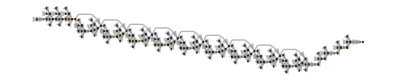

```mathematica
mr=NetInformation[model,"MXNetNodeGraph"]
```

### play with graph

```mathematica
gr=NetInformation[model,"LayersGraph"]
```

-Graphics-

```mathematica
VertexList[gr]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12,1,1},{12,1,2},{12,1,3},{12,1,4},{12,1,5},{12,1,6},{12,1,7},{12,2},{13,1,1},{13,1,2},{13,1,3},{13,1,4},{13,1,5},{13,1,6},{13,1,7},{13,2},{14,1,1},{14,1,2},{14,1,3},{14,1,4},{14,1,5},{14,1,6},{14,1,7},{14,2},{15,1,1},{15,1,2},{15,1,3},{15,1,4},{15,1,5},{15,1,6},{15,1,7},{15,2},{16,1,1},{16,1,2},{16,1,3},{16,1,4},{16,1,5},{16,1,6},{16,1,7},{16,2},{17,1,1},{17,1,2},{17,1,3},{17,1,4},{17,1,5},{17,1,6},{17,1,7},{17,2},{18,1,1},{18,1,2},{18,1,3},{18,1,4},{18,1,5},{18,1,6},{18,1,7},{18,2},{19,1,1},{19,1,2},{19,1,3},{19,1,4},{19,1,5},{19,1,6},{19,1,7},{19,2},{20,1,1},{20,1,2},{20,1,3},{20,1,4},{20,1,5},{20,1,6},{20,1,7},{20,2},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31}}

```mathematica
ConnectedComponents[gr]
```

{{{31}},{{30}},{{29}},{{28}},{{27}},{{26}},{{25}},{{24}},{{23}},{{22}},{{21}},{{20,2}},{{20,1,7}},{{20,1,6}},{{20,1,5}},{{20,1,4}},{{20,1,3}},{{20,1,2}},{{20,1,1}},{{19,2}},{{19,1,7}},{{19,1,6}},{{19,1,5}},{{19,1,4}},{{19,1,3}},{{19,1,2}},{{19,1,1}},{{18,2}},{{18,1,7}},{{18,1,6}},{{18,1,5}},{{18,1,4}},{{18,1,3}},{{18,1,2}},{{18,1,1}},{{17,2}},{{17,1,7}},{{17,1,6}},{{17,1,5}},{{17,1,4}},{{17,1,3}},{{17,1,2}},{{17,1,1}},{{16,2}},{{16,1,7}},{{16,1,6}},{{16,1,5}},{{16,1,4}},{{16,1,3}},{{16,1,2}},{{16,1,1}},{{15,2}},{{15,1,7}},{{15,1,6}},{{15,1,5}},{{15,1,4}},{{15,1,3}},{{15,1,2}},{{15,1,1}},{{14,2}},{{14,1,7}},{{14,1,6}},{{14,1,5}},{{14,1,4}},{{14,1,3}},{{14,1,2}},{{14,1,1}},{{13,2}},{{13,1,7}},{{13,1,6}},{{13,1,5}},{{13,1,4}},{{13,1,3}},{{13,1,2}},{{13,1,1}},{{12,2}},{{12,1,7}},{{12,1,6}},{{12,1,5}},{{12,1,4}},{{12,1,3}},{{12,1,2}},{{12,1,1}},{{11}},{{10}},{{9}},{{8}},{{7}},{{6}},{{5}},{{4}},{{3}},{{2}},{{1}}}

```mathematica
components=ConnectedComponents[gr]
```

{{{31}},{{30}},{{29}},{{28}},{{27}},{{26}},{{25}},{{24}},{{23}},{{22}},{{21}},{{20,2}},{{20,1,7}},{{20,1,6}},{{20,1,5}},{{20,1,4}},{{20,1,3}},{{20,1,2}},{{20,1,1}},{{19,2}},{{19,1,7}},{{19,1,6}},{{19,1,5}},{{19,1,4}},{{19,1,3}},{{19,1,2}},{{19,1,1}},{{18,2}},{{18,1,7}},{{18,1,6}},{{18,1,5}},{{18,1,4}},{{18,1,3}},{{18,1,2}},{{18,1,1}},{{17,2}},{{17,1,7}},{{17,1,6}},{{17,1,5}},{{17,1,4}},{{17,1,3}},{{17,1,2}},{{17,1,1}},{{16,2}},{{16,1,7}},{{16,1,6}},{{16,1,5}},{{16,1,4}},{{16,1,3}},{{16,1,2}},{{16,1,1}},{{15,2}},{{15,1,7}},{{15,1,6}},{{15,1,5}},{{15,1,4}},{{15,1,3}},{{15,1,2}},{{15,1,1}},{{14,2}},{{14,1,7}},{{14,1,6}},{{14,1,5}},{{14,1,4}},{{14,1,3}},{{14,1,2}},{{14,1,1}},{{13,2}},{{13,1,7}},{{13,1,6}},{{13,1,5}},{{13,1,4}},{{13,1,3}},{{13,1,2}},{{13,1,1}},{{12,2}},{{12,1,7}},{{12,1,6}},{{12,1,5}},{{12,1,4}},{{12,1,3}},{{12,1,2}},{{12,1,1}},{{11}},{{10}},{{9}},{{8}},{{7}},{{6}},{{5}},{{4}},{{3}},{{2}},{{1}}}

Construct the condensation of g by finding the edges between the components:

```mathematica
edges=Union[Cases[EdgeList[gr]/.Table[v->First[Select[components,MemberQ[#,v]&]],{v,VertexList[gr]}],u_->v_/;u=!=v]];
```

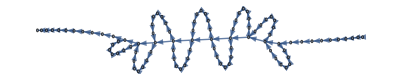

```mathematica
cond=Graph[components,edges]
```

Use the topological ordering of the strongly connected components to order the vertices of g:

```mathematica
tp=TopologicalSort[cond]
```

{{{1}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{11}},{{12,1,1}},{{12,1,2}},{{12,1,3}},{{12,1,4}},{{12,1,5}},{{12,1,6}},{{12,1,7}},{{12,2}},{{13,1,1}},{{13,1,2}},{{13,1,3}},{{13,1,4}},{{13,1,5}},{{13,1,6}},{{13,1,7}},{{13,2}},{{14,1,1}},{{14,1,2}},{{14,1,3}},{{14,1,4}},{{14,1,5}},{{14,1,6}},{{14,1,7}},{{14,2}},{{15,1,1}},{{15,1,2}},{{15,1,3}},{{15,1,4}},{{15,1,5}},{{15,1,6}},{{15,1,7}},{{15,2}},{{16,1,1}},{{16,1,2}},{{16,1,3}},{{16,1,4}},{{16,1,5}},{{16,1,6}},{{16,1,7}},{{16,2}},{{17,1,1}},{{17,1,2}},{{17,1,3}},{{17,1,4}},{{17,1,5}},{{17,1,6}},{{17,1,7}},{{17,2}},{{18,1,1}},{{18,1,2}},{{18,1,3}},{{18,1,4}},{{18,1,5}},{{18,1,6}},{{18,1,7}},{{18,2}},{{19,1,1}},{{19,1,2}},{{19,1,3}},{{19,1,4}},{{19,1,5}},{{19,1,6}},{{19,1,7}},{{19,2}},{{20,1,1}},{{20,1,2}},{{20,1,3}},{{20,1,4}},{{20,1,5}},{{20,1,6}},{{20,1,7}},{{20,2}},{{21}},{{22}},{{23}},{{24}},{{25}},{{26}},{{27}},{{28}},{{29}},{{30}},{{31}}}

```mathematica
h=Graph[Join@@tp,EdgeList[gr],Options[gr]]
```

-Graphics-

## NetModel Metadata

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
NetModel[$ModelNames[[1]],"Properties"]
```

{ByteCount,ConstructionNotebook,ConstructionNotebookExpression,Description,Details,Documentation,DocumentationLink,DownloadedVersion,EvaluationExample,EvaluationNet,ExampleNotebook,ExampleNotebookObject,Hash,InputDomains,Keywords,LatestUpdate,Name,Originator,Performance,Properties,ReleaseDate,SeeAlso,ShortName,SourceMetadata,TaskType,TrainingSetData,TrainingSetInformation,UninitializedEvaluationNet,UUID,Version,WolframLanguageVersionRequired}

```mathematica
NetModel[$ModelNames[[1]],"SourceMetadata"]
```

<|Citation→A. Bulat, G. Tzimiropoulos, "How Far Are We from Solving the 2D & 3D Face Alignment Problem? (And a Dataset of 230,000 3D Facial Landmarks)," arXiv:1703.07332 (2017),Source→https://github.com/1adrianb/2D-and-3D-face-alignment,Rights→[BSD 3-Clause License](https://opensource.org/licenses/BSD-3-Clause),Date→DateObject[{2017},Year,Gregorian,-5.]|>

## Models per Task

```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
modelTask=Table[model->If[NetModel[ model,"TaskType"]==={},"Other",First[NetModel[ model,"TaskType"]]],{model,Keys[$Models]}];
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
Length/@models
```

<|Speech Recognition→1,Other→1,Audio Analysis→2,Object Detection→4,Regression→7,Language Modeling→7,Semantic Segmentation→10,Image Processing→18,Feature Extraction→19,Classification→23|>

```mathematica
models=;
modelTask=;
```

```mathematica
Export["~/model_tasks.csv",modelTask/.Rule->List]
```

~/model_tasks.csv

### To Latex

```mathematica
NetModel[First[Keys[$Models]],"Properties"]
```

{ByteCount,ConstructionNotebook,ConstructionNotebookExpression,Description,Details,Documentation,DocumentationLink,DownloadedVersion,EvaluationExample,EvaluationNet,ExampleNotebook,ExampleNotebookObject,Hash,InputDomains,Keywords,LatestUpdate,Name,Originator,Performance,Properties,ReleaseDate,SeeAlso,ShortName,SourceMetadata,TaskType,TrainingSetData,TrainingSetInformation,UninitializedEvaluationNet,UUID,Version,WolframLanguageVersionRequired}

```mathematica
NetInformation[NetModel[Keys[$Models][[50]]],"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
id=1;
tbl=StringRiffle[
Table[
StringRiffle[{
id++,
NetModel[model,"Name"],
First[NetModel[model,"TaskType"]],
First[NetModel[model,"InputDomains"]],
ToString[Length[$Models[model]]]<>" \\\\ "<>If[!MissingQ[NetModel[model,"SourceMetadata"]["Citation"]]," %"<>StringReplace[NetModel[model,"SourceMetadata"]["Citation"],"\\n"->" "],
""
]
}," & "]
,
{model,Keys[$Models]}
],
"\n"
]
CopyToClipboard[tbl]
```

1 & 2D Face Alignment Net Trained on 300W Large Pose Data & Regression & Image & 967 \\  %A. Bulat, G. Tzimiropoulos, "How Far Are We from Solving the 2D & 3D Face Alignment Problem? (And a Dataset of 230,000 3D Facial Landmarks)," arXiv:1703.07332 (2017)
2 & 3D Face Alignment Net Trained on 300W Large Pose Data & Regression & Image & 967 \\  %A. Bulat, G. Tzimiropoulos, "How Far Are We from Solving the 2D & 3D Face Alignment Problem? (And a Dataset of 230,000 3D Facial Landmarks)," arXiv:1703.07332 (2017)
3 & AdaIN-Style Trained on MS-COCO and Painter by Numbers Data & Image Processing & Image & 109 \\  %X. Huang, S. Belongie, "Arbitrary Style Transfer in Real-Time with Adaptive Instance Normalization," arXiv:1703.06868 (2017)
4 & Ademxapp Model A1 Trained on ADE20K Data & Semantic Segmentation & Image & 141 \\  %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
5 & Ademxapp Model A1 Trained on Cityscapes Data & Semantic Segmentation & Image & 141 \\  %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
6 & Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data & Semantic Segmentation & Image & 141 \\  %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
7 & Ademxapp Model A Trained on ImageNet Competition Data & Classification & Image & 142 \\  %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
8 & Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data & Classification & Image & 40 \\  %R. Rothe, R. Timofte, L. Van Gool, "Deep Expectation of Real and Apparent Age from a Single Image without Facial Landmarks," International Journal of Computer Vision (IJCV) (2016)
9 & Age Estimation VGG-16 Trained on IMDB-WIKI Data & Classification & Image & 40 \\  %R. Rothe, R. Timofte, L. Van Gool, "Deep Expectation of Real and Apparent Age from a Single Image without Facial Landmarks," International Journal of Computer Vision (IJCV) (2016)
10 & BERT Trained on BookCorpus and English Wikipedia Data & Feature Extraction & Text & 862 \\  %J. Devlin, M.-W. Chang, K. Lee, K. Toutanova, "BERT: Pre-training of Deep Bidirectional Transformers for Language Understanding," arXiv:1810.04805 (2018)
11 & BPEmb Subword Embeddings Trained on Wikipedia Data & Feature Extraction & Text & 1 \\  %B. Heinzerling, M. Strube, "BPEmb: Tokenization-free Pre-trained Subword Embeddings in 275 Languages," arXiv:1710.02187 (2017)
12 & CapsNet Trained on MNIST Data & Classification & Image & 53 \\  %S. Sabour, N. Frosst, G. E. Hinton, "Dynamic Routing between Capsules," arXiv:1710.09829 (2017)
13 & Clinical Concept Embeddings Trained on Health Insurance Claims, Clinical Narratives from Stanford and PubMed Journal Articles & Feature Extraction & Text & 1 \\  %A.L. Beam et al., 
"Clinical Concept Embeddings Learned from Massive Sources of Multimodal Medical Data," arXiv:1804.01486 (2018)
14 & Colorful Image Colorization Trained on ImageNet Competition Data & Image Processing & Image & 58 \\  %R. Zhang, P. Isola, A. Efros, "Colorful Image Colorization," arXiv:1603.08511v5 (2016)
15 & ColorNet Image Colorization Trained on ImageNet Competition Data & Image Processing & Image & 62 \\  %S. Iizuka, E. Simo-Serra, H. Ishikawa, "Let There Be Color!: Joint End-to-End Learning of Global and Local Image Priors for Automatic Image Colorization with Simultaneous Classification," ACM Transactions on Graphics (Proc. of SIGGRAPH 2016) 35(4) (2016)
16 & ColorNet Image Colorization Trained on Places Data & Image Processing & Image & 62 \\  %S. Iizuka, E. Simo-Serra, H. Ishikawa, "Let There Be Color!: Joint End-to-End Learning of Global and Local Image Priors for Automatic Image Colorization with Simultaneous Classification," ACM Transactions on Graphics (Proc. of SIGGRAPH 2016) 35(4) (2016)
17 & ConceptNet Numberbatch Word Vectors V17.06 & Feature Extraction & Text & 1 \\  %R. Speer, J. Chin, C. Havasi, "ConceptNet 5.5: An Open Multilingual Graph of General Knowledge," arXiv:1612.03975 (2016)
18 & ConceptNet Numberbatch Word Vectors V17.06 (Raw Model) & Feature Extraction & Text & 1 \\  %R. Speer, J. Chin, C. Havasi, "ConceptNet 5.5: An Open Multilingual Graph of General Knowledge," arXiv:1612.03975 (2016)
19 & CREPE Pitch Detection Net Trained on Monophonic Signal Data & Audio Analysis & Audio & 35 \\  %J. W. Kim, J. Salamon, P. Li, J. P. Bello, "CREPE: A Convolutional Representation for Pitch Estimation," arXiv:1802.06182 (2018)
20 & CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
21 & CycleGAN Horse-to-Zebra Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
22 & CycleGAN Monet-to-Photo Translation & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
23 & CycleGAN Orange-to-Apple Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
24 & CycleGAN Photo-to-Cezanne Translation & Image Processing & Image & 96 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
25 & CycleGAN Photo-to-Monet Translation & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
26 & CycleGAN Photo-to-Van Gogh Translation & Image Processing & Image & 96 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
27 & CycleGAN Summer-to-Winter Translation & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
28 & CycleGAN Winter-to-Summer Translation & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
29 & CycleGAN Zebra-to-Horse Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\  %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
30 & Deep Speech 2 Trained on Baidu English Data & Speech Recognition & Audio & 152 \\  %D. Amodei et al., "Deep Speech 2: End-to-End Speech Recognition in English and Mandarin," arXiv:1512.02595 (2015)
31 & Dilated ResNet-105 Trained on Cityscapes Data & Semantic Segmentation & Image & 360 \\  %F. Yu, V. Koltun, T. Funkhouser, "Dilated Residual Networks," arXiv:1705.09914 (2017)
32 & Dilated ResNet-22 Trained on Cityscapes Data & Semantic Segmentation & Image & 86 \\  %F. Yu, V. Koltun, T. Funkhouser, "Dilated Residual Networks," arXiv:1705.09914 (2017)
33 & Dilated ResNet-38 Trained on Cityscapes Data & Semantic Segmentation & Image & 142 \\  %F. Yu, V. Koltun, T. Funkhouser, "Dilated Residual Networks," arXiv:1705.09914 (2017)
34 & ELMo Contextual Word Representations Trained on 1B Word Benchmark & Feature Extraction & Text & 111 \\  %M. E. Peters, M. Neumann, M. Iyyer, M. Gardner, C. Clark, K. Lee, L. Zettlemoyer, "Deep Contextualized Word Representations," arXiv:1802.05365 NAACL(2018)
35 & Enhanced Super-Resolution GAN Trained on DIV2K, Flickr2K and OST Data & Image Processing & Image & 1093 \\  %X. Wang, K. Yu, S. Wu, J. Gu, Y. Liu, C. Dong, Y. Qiao, C. C. Loy, X. Tang, "ESRGAN: Enhanced Super-Resolution Generative Adversarial Networks," arXiv:1809.00219 (2018)
36 & Gender Prediction VGG-16 Trained on IMDB-WIKI Data & Classification & Image & 40 \\  %R. Rothe, R. Timofte, L. Van Gool, "Deep Expectation of Real and Apparent Age from a Single Image without Facial Landmarks," International Journal of Computer Vision (IJCV) (2016)
37 & GloVe 100-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
38 & GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
39 & GloVe 200-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
40 & GloVe 25-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
41 & GloVe 300-Dimensional Word Vectors Trained on Common Crawl 42B & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
42 & GloVe 300-Dimensional Word Vectors Trained on Common Crawl 840B & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
43 & GloVe 300-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
44 & GloVe 50-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
45 & GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data & Feature Extraction & Text & 1 \\  %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
46 & GPT-2 Transformer Trained on WebText Data & Language Modeling & Text & 832 \\  %A. Radford, J. Wu, R. Child, D. Luan, D. Amodei, I. Sutskever, "Language Models are Unsupervised Multitask Learners" (2019)
47 & GPT Transformer Trained on BookCorpus Data & Feature Extraction & Text & 857 \\  %A. Radford, K. Narasimhan, T. Salimans, I. Sutskever, "Improving language understanding by generative pre-training," preprint (2018)
48 & Inception V1 Trained on Extended Salient Object Subitizing Data & Classification & Image & 147 \\  %J. Zhang, S. Ma, M. Sameki, S. Sclaroff, M. Betke, Z. Lin, X. Shen, B. Price, R. Mech, "Salient Object Subitizing," arXiv:1607.07525 (2016)
49 & Inception V1 Trained on ImageNet Competition Data & Classification & Image & 147 \\  %C. Szegedy, W. Liu, Y. Jia, P. Sermanet, S. Reed, D. Anguelov, D. Erhan, V. Vanhoucke, A. Rabinovich, "Going Deeper with Convolutions," arXiv:1409.4842 (2014)
50 & Inception V1 Trained on Places365 Data & Classification & Image & 147 \\  %B. Zhou, A. Khosla, A. Lapedriza, A. Torralba, A. Oliva, "Places: An Image Database for Deep Scene Understanding," arXiv:1610.02055 (2016)
51 & Inception V3 Trained on ImageNet Competition Data & Classification & Image & 311 \\  %C. Szegedy, V. Vanhoucke, S. Ioffe, J. Shlens, Z. Wojna, "Rethinking the Inception Architecture for Computer Vision," arXiv:1512.00567 (2015)
52 & LeNet Trained on MNIST Data & Classification & Image & 11 \\  %Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998)
53 & MobileNet V2 Trained on ImageNet Competition Data & Classification & Image & 153 \\  %M. Sandler, A. Howard, M. Zhu, A. Zhmoginov, L. C. Chen, "MobileNetV2: Inverted Residuals and Linear Bottlenecks," arXiv:1801.04381 (2018)
54 & Multi-scale Context Aggregation Net Trained on CamVid Data & Semantic Segmentation & Image & 53 \\  %F. Yu, V. Koltun, "Multi-scale Context Aggregation by Dilated Convolutions," arXiv:1511.07122 (2016)
55 & Multi-scale Context Aggregation Net Trained on Cityscapes Data & Semantic Segmentation & Image & 58 \\  %F. Yu, V. Koltun, "Multi-scale Context Aggregation by Dilated Convolutions," arXiv:1511.07122 (2016)
56 & Multi-scale Context Aggregation Net Trained on PASCAL VOC2012 Data & Semantic Segmentation & Image & 53 \\  %F. Yu, V. Koltun, "Multi-scale Context Aggregation by Dilated Convolutions," arXiv:1511.07122 (2016)
57 & OpenFace Face Recognition Net Trained on CASIA-WebFace and FaceScrub Data & Feature Extraction & Image & 172 \\  %F. Schroff, D. Kalenichenko, J. Philbin, "FaceNet: A Unified Embedding for Face Recognition and Clustering," arXiv: 1503.03832 (2015)
58 & Pix2pix Photo-to-Street-Map Translation & Image Processing & Image & 56 \\  %P. Isola, J. Zhu, T. Zhou, A. A. Efros, "Image-to-Image Translation with Conditional Adversarial Networks," arXiv:1611.07004 (2016)
59 & Pix2pix Street-Map-to-Photo Translation & Image Processing & Image & 56 \\  %P. Isola, J. Zhu, T. Zhou, A. A. Efros, "Image-to-Image Translation with Conditional Adversarial Networks," arXiv:1611.07004 (2016)
60 & ResNet-101 Trained on Augmented CASIA-WebFace Data & Feature Extraction & Image & 345 \\  %I. Masi, A. T. Tran, T. Hassner, J. T. Leksut, G. Medioni, "Do We Really Need to Collect Millions of Faces for Effective Face Recognition?," European Conference on Computer Vision (2016)
61 & ResNet-101 Trained on ImageNet Competition Data & Classification & Image & 347 \\  %K. He, X. Zhang, S. Ren, J. Sun, "Deep Residual Learning for Image Recognition," arXiv:1512.03385 (2015)
62 & ResNet-101 Trained on YFCC100m Geotagged Data & Classification & Image & 344 \\ 
63 & ResNet-152 Trained on ImageNet Competition Data & Classification & Image & 517 \\  %K. He, X. Zhang, S. Ren, J. Sun, "Deep Residual Learning for Image Recognition," arXiv:1512.03385 (2015)
64 & ResNet-50 Trained on ImageNet Competition Data & Classification & Image & 177 \\  %K. He, X. Zhang, S. Ren, J. Sun, "Deep Residual Learning for Image Recognition," arXiv:1512.03385 (2015)
65 & Self-Normalizing Net for Numeric Data & Classification & Numeric & 23 \\  %K. Günter, T. Unterthiner, A. Mayr, S. Hochreiter, "Self-Normalizing Neural Networks," arXiv:1706.02515 (2017)
66 & Sentiment Language Model Trained on Amazon Product Review Data & Language Modeling & Text & 23 \\  %A. Radford, R. Jozefowicz, I. Sutskever, "Learning to Generate Reviews and Discovering Sentiment,"  arXiv:1704.01444 (2017)
67 & Single-Image Depth Perception Net Trained on Depth in the Wild Data & Regression & Image & 501 \\  %W. Chen, Z. Fu, D. Yang and J. Deng, "Single-Image Depth Perception in the Wild," arXiv:1604.03901 (2016)
68 & Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data & Regression & Image & 501 \\  %W. Chen, Z. Fu, D. Yang and J. Deng, "Single-Image Depth Perception in the Wild," arXiv:1604.03901 (2016)
69 & Single-Image Depth Perception Net Trained on NYU Depth V2 Data & Regression & Image & 501 \\  %W. Chen, Z. Fu, D. Yang, J. Deng, "Single-Image Depth Perception in the Wild," arXiv:1604.03901 (2016)
70 & Squeeze-and-Excitation Net Trained on ImageNet Competition Data & Classification & Image & 874 \\  %J. Hu, L. Shen, S. Albanie, G. Sun, E. Wu, "Squeeze-and-Excitation Networks," arXiv:1709.01507 (2018)
71 & SqueezeNet V1.1 Trained on ImageNet Competition Data & Classification & Image & 69 \\  %F. N. Iandola, S. Han, M. W. Moskewicz, K. Ashraf, W. J. Dally, K. Keutzer, "SqueezeNet: AlexNet-Level Accuracy with 50x Fewer Parameters and <0.5MB Model Size," arXiv:1602.07360 (2016)
72 & SSD-VGG-300 Trained on PASCAL VOC Data & Object Detection & Image & 145 \\  %W. Liu, et al. "SSD: Single shot multibox detector," arXiv:1512.02325v5 (2016)
73 & SSD-VGG-512 Trained on MS-COCO Data & Object Detection & Image & 157 \\  %W. Liu, et al. "SSD: Single shot multibox detector," arXiv:1512.02325v5 (2016)
74 & SSD-VGG-512 Trained on PASCAL VOC2007, PASCAL VOC2012 and MS-COCO Data & Object Detection & Image & 157 \\  %W. Liu, et al. "SSD: Single shot multibox detector," arXiv:1512.02325v5 (2016)
75 & U-Net Trained on Glioblastoma-Astrocytoma U373 Cells on a Polyacrylamide Substrate Data & Semantic Segmentation & Image & 61 \\  %O. Ronneberger, P. Fischer, T. Brox "U-Net: Convolutional Networks for Biomedical Image Segmentation," arXiv:1505.04597 (2015)
76 & Unguided Volumetric Regression Net for 3D Face Reconstruction & Regression & Image & 1029 \\  %A. S. Jackson, A. Bulat, V. Argyriou, G. Tzimiropoulos, "Large Pose 3D Face Reconstruction from a Single Image via Direct Volumetric CNN Regression," arXiv:1703.07834 (2017)
77 & Vanilla CNN for Facial Landmark Regression & Regression & Image & 24 \\  %Y. Wu, T. Hassner, K. Kim, G. Medioni, P. Natarajan, "Facial Landmark Detection with Tweaked Convolutional Neural Networks," arXiv:1511.04031 (2015)
78 & Very Deep Net for Super-Resolution & Image Processing & Image & 40 \\  %J. Kim, J. Kwon Lee and K. Mu Lee, "Accurate Image Super-Resolution Using Very Deep Convolutional Networks," Proc. of IEEE Conference on Computer Vision and Pattern Recognition (CVPR) (2016)
79 & VGG-16 Trained on ImageNet Competition Data & Classification & Image & 40 \\  %K. Simonyan, A. Zisserman, "Very Deep Convolutional Networks for Large-Scale Image Recognition," arXiv:1409.1556 (2014)
80 & VGG-19 Trained on ImageNet Competition Data & Classification & Image & 46 \\  %K. Simonyan, A. Zisserman, "Very Deep Convolutional Networks for Large-Scale Image Recognition," arXiv:1409.1556 (2014)
81 & VGGish Feature Extractor Trained on YouTube Data & Feature Extraction & Audio & 25 \\  %S. Hershey, S. Chaudhuri, D. P. W. Ellis, J. F. Gemmeke, A. Jansen, R. C. Moore, M. Plakal, D. Platt, R. A. Saurous, B. Seybold, M. Slaney, R. J. Weiss, K. Wilson, "CNN Architectures for Large-Scale Audio Classification," arXiv:1609.09430 (2017)
82 & Wide ResNet-50-2 Trained on ImageNet Competition Data & Classification & Image & 176 \\  %S. Zagoruyko, N. Komodakis, "Wide Residual Networks,"  arXiv:1605.07146v4 (2017)
83 & Wolfram AudioIdentify V1 Trained on AudioSet Data & Audio Analysis & Audio & 156 \\  %Wolfram Research
84 & Wolfram C Character-Level Language Model V1 & Language Modeling & Text & 8 \\  %Wolfram Research
85 & Wolfram English Character-Level Language Model V1 & Language Modeling & Text & 8 \\  %Wolfram Research
86 & Wolfram ImageIdentify Net V1 & Classification & Image & 232 \\  %Wolfram Research
87 & Wolfram JavaScript Character-Level Language Model V1 & Language Modeling & Text & 7 \\  %Wolfram Research
88 & Wolfram LaTeX Character-Level Language Model V1 & Language Modeling & Text & 7 \\  %Wolfram Research
89 & Wolfram Python Character-Level Language Model V1 & Language Modeling & Text & 8 \\  %Wolfram Research
90 & Yahoo Open NSFW Model V1 & Classification & Image & 177 \\ 
91 & YOLO V2 Trained on MS-COCO Data & Object Detection & Image & 106 \\  %J. Redmon, A. Farhadi, "YOLO9000: Better, Faster, Stronger," arXiv:1612.08242 (2016)

## Model Layer Distribution

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
```

```mathematica
models=<|"all_tasks"->Keys[$Models]|>;
```

```mathematica
shorten[s_]:=StringReplace[SymbolName[s],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Deconvolution"->"Dconv","GatedRecurrent"->"GR","Aggregation"->"Agg","ConstantPlus"->"Pls","ConstantTimes"->"Tms","Flatten"->"Flt","Softmax"->"Sfm","Total"->"Red","Dropout"->"Drp","Pooling"->"Pol","Reshape"->"Rshp","Catenate"->"Cat","LocalResponseNormalization"->"LRN"}];
noshorten[s_]:=StringReplace[SymbolName[s],{"Layer"->"","Normalization"->"Norm","BatchNormalization"->"BatchNorm","LocalResponseNormalization"->"LocalRespNorm","GatedRecurrent"->"GatedRecurr","ConstantPlus"->"ConstPlus","ConstantTimes"->"ConstTimes","Deconvolution"->"Deconv"}]
```

```mathematica
figs=Association@Table[
task=task0;
ms=Lookup[$Models,models[task]];
(*layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];*)
layers=KeySelect[Counts[Flatten[ms][[All,0,1]]],#=!=ConstantArrayLayer&&!StringContainsQ[SymbolName[#],"Sequence"]&];
data=ReverseSort[layers];
task->BarChart[
data,
ChartLabels->Map[Rotate[Style[ noshorten[#],FontSize->18,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[data]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
(*PlotLabel->task<>" Task"*)
],
{task0,Keys[models]}
];
```

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"figs","layer_distribution_per_task"}];
Quiet[CreateDirectory[baseDir]];
Table[Export[FileNameJoin[{baseDir,StringReplace[key," "->"_"]<>".pdf"}], figs[key],ImageSize->Scaled[1.2],ImageResolution->300],{key,Keys[figs]}]
```

{/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/all_tasks.pdf}

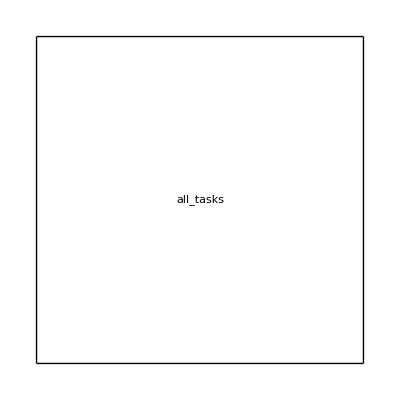

```mathematica
GraphicsGrid[Partition[Table[Labeled[figs[key],key],{key,Keys[figs]}],UpTo[3]],Frame->All,ImageMargins->0, ImageSize->Scaled[0.75]]
```

```mathematica
export
```

```mathematica
Import["http://tinyurl.com/ntmhkca"]
```

```mathematica
layers
```

<|ConvolutionLayer→1207,BatchNormalizationLayer→929,ElementwiseLayer→1284|>

```mathematica
tasks=Union[Flatten[Map[NetModel[ #,"TaskType"]&,Keys[$Models]]]]
```

{Audio Analysis,Classification,Feature Extraction,Image Processing,Language Modeling,Object Detection,Regression,Semantic Segmentation,Speech Recognition}

```mathematica
task="Object Detection";
ms=Lookup[$Models,models[task]];
layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];
ms=Association[Table[model->With[{info=Counts[Flatten[$Models[model]][[All,0,1]]]},Table[Lookup[info,layer,0],{layer,Keys[layers]}]],{model,models[task]}]];
```

```mathematica
Keys[models]
```

{Speech Recognition,Audio Analysis,Object Detection,Regression,Language Modeling,Semantic Segmentation,Image Processing,Feature Extraction,Classification}

```mathematica
Keys[layers]
```

{ElementwiseLayer,LinearLayer,DotLayer,ConvolutionLayer,BatchNormalizationLayer}

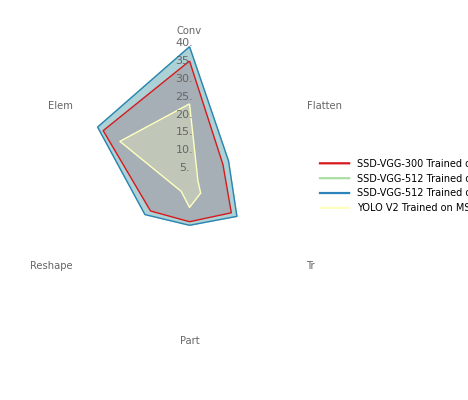

```mathematica
Needs["RadarChart`"]
RadarChart[Values[ms],Filling->Axis,AxesLabel->Map[Style[StringReplace[SymbolName[#],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}],FontSize->10,FontFamily->"Latin Modern Roman"]&,Keys[layers]],PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1]},ChartLegends->Keys[ms]]
```

## Model Layer Distribution By Task

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
shorten[s_]:=StringReplace[SymbolName[s],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Deconvolution"->"Dconv","GatedRecurrent"->"GR","Aggregation"->"Agg","ConstantPlus"->"Pls","ConstantTimes"->"Tms","Flatten"->"Flt","Softmax"->"Sfm","Total"->"Red","Dropout"->"Drp","Pooling"->"Pol","Reshape"->"Rshp","Catenate"->"Cat","LocalResponseNormalization"->"LRN"}];
noshorten[s_]:=StringReplace[SymbolName[s],{"Layer"->"","Normalization"->"Norm","BatchNormalization"->"BatchNorm","LocalResponseNormalization"->"LocalRespNorm","GatedRecurrent"->"GatedRecurr","ConstantPlus"->"ConstPlus","ConstantTimes"->"ConstTimes","Deconvolution"->"Deconv"}]
```

```mathematica
figs=Association@Table[
task=task0;
ms=Lookup[$Models,models[task]];
(*layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];*)
layers=KeySelect[Counts[Flatten[ms][[All,0,1]]],#=!=ConstantArrayLayer&&!StringContainsQ[SymbolName[#],"Sequence"]&];
data=ReverseSort[layers];
task->BarChart[
data,
ChartLabels->Map[Rotate[Style[ noshorten[#],FontSize->26,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[data]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
(*PlotLabel->task<>" Task"*)
],
{task0,Keys[models]}
];
```

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"figs","layer_distribution_per_task"}];
Quiet[CreateDirectory[baseDir]];
Table[Export[FileNameJoin[{baseDir,StringReplace[key," "->"_"]<>".pdf"}], figs[key],ImageSize->Scaled[1.2],ImageResolution->300],{key,Keys[figs]}]
```

{/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Speech_Recognition.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Audio_Analysis.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Object_Detection.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Regression.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Language_Modeling.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Semantic_Segmentation.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Image_Processing.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Feature_Extraction.pdf,/Users/abduld/papers/synthetic_benchmark_code/figs/layer_distribution_per_task/Classification.pdf}

```mathematica
GraphicsGrid[Partition[Table[Labeled[figs[key],key],{key,Keys[figs]}],UpTo[3]],Frame->All,ImageMargins->0, ImageSize->Scaled[0.75]]
```

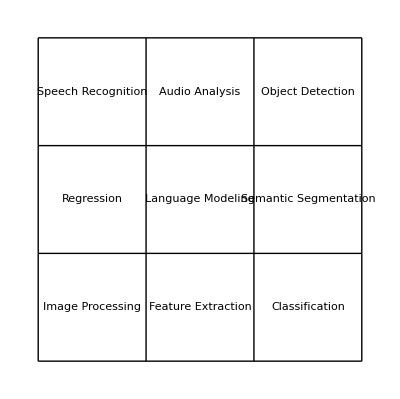

```mathematica
export
```

```mathematica
Import["http://tinyurl.com/ntmhkca"]
```

```mathematica
layers
```

<|ConvolutionLayer→1207,BatchNormalizationLayer→929,ElementwiseLayer→1284|>

```mathematica
tasks=Union[Flatten[Map[NetModel[ #,"TaskType"]&,Keys[$Models]]]]
```

{Audio Analysis,Classification,Feature Extraction,Image Processing,Language Modeling,Object Detection,Regression,Semantic Segmentation,Speech Recognition}

```mathematica
task="Object Detection";
ms=Lookup[$Models,models[task]];
layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];
ms=Association[Table[model->With[{info=Counts[Flatten[$Models[model]][[All,0,1]]]},Table[Lookup[info,layer,0],{layer,Keys[layers]}]],{model,models[task]}]];
```

```mathematica
Keys[models]
```

{Speech Recognition,Audio Analysis,Object Detection,Regression,Language Modeling,Semantic Segmentation,Image Processing,Feature Extraction,Classification}

```mathematica
Keys[layers]
```

{ElementwiseLayer,LinearLayer,DotLayer,ConvolutionLayer,BatchNormalizationLayer}

```mathematica
Needs["RadarChart`"]
RadarChart[Values[ms],Filling->Axis,AxesLabel->Map[Style[StringReplace[SymbolName[#],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}],FontSize->10,FontFamily->"Latin Modern Roman"]&,Keys[layers]],PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1]},ChartLegends->Keys[ms]]
```

-Graphics-

## Model Layer Distribution

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

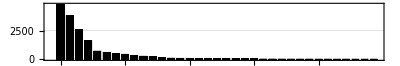

```mathematica
data=ReverseSort[Counts[Flatten[Values[$Models]][[All,0,1]]]];
BarChart[
data,
ChartLabels->Map[Rotate[Style[#,FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[data]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

## Within Model Sharing

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
xModels=Keys[SyntheticBenchmark`Assets`Models`$Models];
ClearAll[getModelId];
getModelId[name_]:=First[FirstPosition[xModels,name]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

```mathematica
unq=Association@KeyValueMap[
Function[{key,val},
key->{Length[val],Length[Union[val]],N[Length[Union[val]]/Length[val]]}
],
$Models
];
```

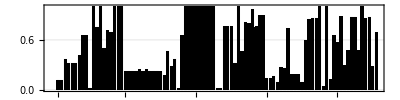

```mathematica
fig=BarChart[
MapThread[Tooltip,{Values[unq][[All,-1]],Keys[unq]}],
BarSpacing->{0.5,0},
ChartLabels->Map[Rotate[Style[If[Mod[getModelId[#],5]===0||getModelId[#]===1, getModelId[#],""],FontSize->32,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[unq]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->32}
]
```

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"figs"}];
Quiet[CreateDirectory[baseDir]];
Export[FileNameJoin[{baseDir,"within_model_sharing.pdf"}], fig,ImageSize->Scaled[1.2],ImageResolution->300]
```

/Users/abduld/papers/synthetic_benchmark_code/figs/within_model_sharing.pdf

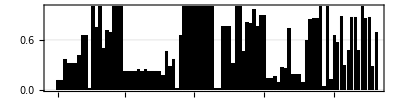

```mathematica
BarChart[
MapThread[Tooltip,{Values[unq][[All,-1]],Keys[unq]}],
BarSpacing->{0.5,0},
ChartLabels->Map[Rotate[Style[If[Mod[getModelId[#],5]===0||getModelId[#]===1, getModelId[#],""],FontSize->8,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[unq]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8}
]
```

```mathematica
Grid[Normal[Select[unq,#[[-1]]<0.5&]]/.HoldPattern[Rule[x__]]:>Flatten[List[x]],Frame->All]
```

2D Face Alignment Net Trained on 300W Large Pose Data | 967 | 112 | 0.115822
3D Face Alignment Net Trained on 300W Large Pose Data | 967 | 112 | 0.115822
AdaIN-Style Trained on MS-COCO and Painter by Numbers Data | 109 | 40 | 0.366972
Ademxapp Model A1 Trained on ADE20K Data | 141 | 45 | 0.319149
Ademxapp Model A1 Trained on Cityscapes Data | 141 | 45 | 0.319149
Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data | 141 | 45 | 0.319149
Ademxapp Model A Trained on ImageNet Competition Data | 142 | 58 | 0.408451
BERT Trained on BookCorpus and English Wikipedia Data | 862 | 19 | 0.0220418
CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Horse-to-Zebra Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Monet-to-Photo Translation | 94 | 21 | 0.223404
CycleGAN Orange-to-Apple Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Photo-to-Cezanne Translation | 96 | 23 | 0.239583
CycleGAN Photo-to-Monet Translation | 94 | 21 | 0.223404
CycleGAN Photo-to-Van Gogh Translation | 96 | 23 | 0.239583
CycleGAN Summer-to-Winter Translation | 94 | 21 | 0.223404
CycleGAN Winter-to-Summer Translation | 94 | 21 | 0.223404
CycleGAN Zebra-to-Horse Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
Deep Speech 2 Trained on Baidu English Data | 152 | 33 | 0.217105
Dilated ResNet-105 Trained on Cityscapes Data | 360 | 60 | 0.166667
Dilated ResNet-22 Trained on Cityscapes Data | 86 | 40 | 0.465116
Dilated ResNet-38 Trained on Cityscapes Data | 142 | 40 | 0.28169
ELMo Contextual Word Representations Trained on 1B Word Benchmark | 111 | 41 | 0.369369
Enhanced Super-Resolution GAN Trained on DIV2K, Flickr2K and OST Data | 1093 | 17 | 0.0155535
GPT-2 Transformer Trained on WebText Data | 832 | 14 | 0.0168269
GPT Transformer Trained on BookCorpus Data | 857 | 15 | 0.0175029
Inception V3 Trained on ImageNet Competition Data | 311 | 100 | 0.321543
MobileNet V2 Trained on ImageNet Competition Data | 153 | 70 | 0.457516
ResNet-101 Trained on Augmented CASIA-WebFace Data | 345 | 46 | 0.133333
ResNet-101 Trained on ImageNet Competition Data | 347 | 48 | 0.138329
ResNet-101 Trained on YFCC100m Geotagged Data | 344 | 56 | 0.162791
ResNet-152 Trained on ImageNet Competition Data | 517 | 48 | 0.0928433
ResNet-50 Trained on ImageNet Competition Data | 177 | 48 | 0.271186
Self-Normalizing Net for Numeric Data | 23 | 6 | 0.26087
Single-Image Depth Perception Net Trained on Depth in the Wild Data | 501 | 90 | 0.179641
Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data | 501 | 90 | 0.179641
Single-Image Depth Perception Net Trained on NYU Depth V2 Data | 501 | 90 | 0.179641
Squeeze-and-Excitation Net Trained on ImageNet Competition Data | 874 | 82 | 0.0938215
Unguided Volumetric Regression Net for 3D Face Reconstruction | 1029 | 40 | 0.0388727
Very Deep Net for Super-Resolution | 40 | 5 | 0.125
Wide ResNet-50-2 Trained on ImageNet Competition Data | 176 | 51 | 0.289773
Wolfram AudioIdentify V1 Trained on AudioSet Data | 156 | 73 | 0.467949
Wolfram ImageIdentify Net V1 | 232 | 109 | 0.469828
Yahoo Open NSFW Model V1 | 177 | 49 | 0.276836

```mathematica
Length[Union[$Models["MobileNet V2 Trained on ImageNet Competition Data"]]]/N@Length[$Models["MobileNet V2 Trained on ImageNet Competition Data"]]
```

0.457516

## Model Sharing across networks

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
$ModelNames=Keys[$Models];
MapIndexed[Rule,Keys[$Models]];
```

```mathematica
resnet50=$Models[[65]];
resnet50Name="ResNet-50 Trained on ImageNet Competition Data";
inceptionv3=$Models[[51]];
inceptionv3Name="Inception V3 Trained on ImageNet Competition Data";
```

```mathematica
Length[Union[resnet50]]+Length[Union[inceptionv3]]
```

148

```mathematica
Length[Union[Flatten[{resnet50,inceptionv3}]]]
```

147

```mathematica
Keys[models]
```

{Speech Recognition,Other,Audio Analysis,Object Detection,Regression,Language Modeling,Semantic Segmentation,Image Processing,Feature Extraction,Classification}

### for some task type do

```mathematica
taskType="Classification";
taskType="Object Detection";
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

### for all models do

for all models do

```mathematica
taskType="All";
```

```mathematica
models=<|"All"->SortBy[Keys[$Models],getModelId]|>;
```

### and then run

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
xModels=Keys[SyntheticBenchmark`Assets`Models`$Models];
ClearAll[getModelId];getModelId[name_]:=First[FirstPosition[xModels,name]]
```

```mathematica
(*models=<|"All"->SortBy[Keys[$Models[[;;30]]],getModelId]|>;*)
```

```mathematica
data=Table[
k1=tuples[[1]];
k2=tuples[[2]];
m1=$Models[k1];
m2=$Models[k2];
Length[Intersection[m1,m2]]/Length[DeleteDuplicates[Flatten[{m1,m2}]]],
{tuples,Tuples[models[taskType],{2}]}
];
```

```mathematica
cf=Switch[#,
Infinity,White,
0,
Black,
_,
(*"DarkRainbow"~Blend~#*)
RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745]
]&;
```

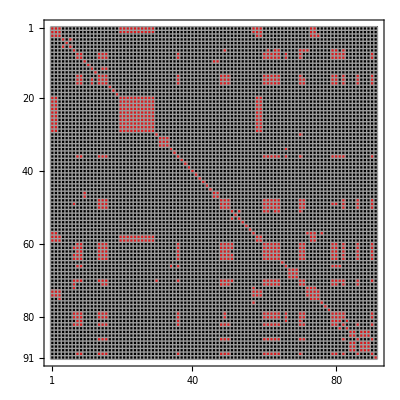

```mathematica
fig=ArrayPlot[Partition[data,Length[models[taskType]]],ColorFunction->cf,Frame->True,Mesh->True,ImageSize->Scaled[0.5],FrameTicksStyle->Opacity[1],FrameTicks->All,ImageMargins->0,
PlotTheme->"Grid",
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->32}
]
```

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"figs"}];
Quiet[CreateDirectory[baseDir]];
Export[FileNameJoin[{baseDir,"across_model_sharing.pdf"}], fig,ImageSize->Scaled[1.2],ImageResolution->300]
```

/Users/abduld/papers/synthetic_benchmark_code/figs/across_model_sharing.pdf

```mathematica
ArrayPlot[Partition[data,Length[models[taskType]]],Mesh->False,Frame->True,PlotLegends->Automatic,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->All]
```

-Graphics-

### analysis

```mathematica
es=Partition[data,Length[models[taskType]]];
ps=Flatten@Table[
If[ii=!=jj&&ii<jj&&Abs[ii-jj]>2&&es[[ii,jj]]>0.5,
{ii,jj}->N[es[[ii,jj]]],
Nothing
],
{ii,Length[models[taskType]]},{jj,Length[models[taskType]]}
]
```

{{8,36}→0.857143,{8,79}→0.857143,{8,80}→0.857143,{9,36}→0.857143,{9,79}→0.857143,{9,80}→0.857143,{20,23}→1.,{20,24}→0.76,{20,25}→1.,{20,26}→0.76,{20,27}→1.,{20,28}→1.,{20,29}→1.,{21,24}→0.76,{21,25}→1.,{21,26}→0.76,{21,27}→1.,{21,28}→1.,{21,29}→1.,{22,25}→1.,{22,26}→0.76,{22,27}→1.,{22,28}→1.,{22,29}→1.,{23,26}→0.76,{23,27}→1.,{23,28}→1.,{23,29}→1.,{24,27}→0.76,{24,28}→0.76,{24,29}→0.76,{25,28}→1.,{25,29}→1.,{26,29}→0.76,{36,79}→0.857143,{36,80}→0.857143,{60,63}→0.958333,{60,64}→0.958333,{61,64}→1.,{84,87}→0.75,{84,89}→1.,{85,89}→1.}

### ignoring input and output shape

```mathematica
removeInputOutputSize[lyr_[assoc_,r___]]:=lyr[Append[assoc,"Parameters"->KeyDrop[assoc["Parameters"],{"$SpatialDimensions","$InputChannels","$InputSize","$OutputSize"}]]]
```

```mathematica
data=Table[
k1=tuples[[1]];
k2=tuples[[2]];
m1=removeInputOutputSize/@$Models[k1];
m2=removeInputOutputSize/@$Models[k2];
Length[DeleteDuplicates[Flatten[{m1,m2}]]]/(Length[DeleteDuplicates[m1]]+Length[DeleteDuplicates[m2]]),
{tuples,Tuples[models["Classification"],{2}]}
];
```

```mathematica
m1[[;;2]]
```

{ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{3,224,224},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→64,KernelSize→{7,7},Stride→{2,2},PaddingSize→{{3,3},{3,3}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→3|>|>],BatchNormalizationLayer[<|Type→BatchNormalization,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Parameters→<|Momentum→0.9,Epsilon→0.0001,$Channels→64,Interleaving→False|>|>]}

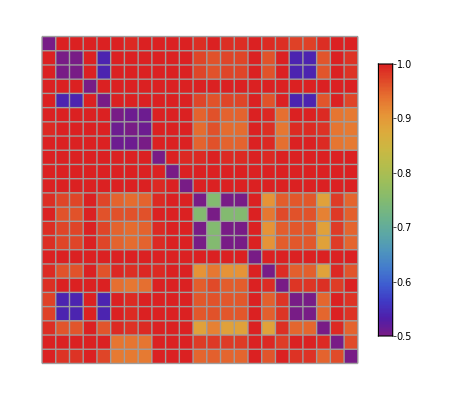

```mathematica
ArrayPlot[Partition[data,Length[models["Classification"]]],ColorFunction->"Rainbow",Mesh->True,PlotLegends->Automatic,ImageSize->Scaled[0.5]]
```

```mathematica
$Models[models["Classification"][[;;2]]]
```

Missing[KeyAbsent,{Ademxapp Model A Trained on ImageNet Competition Data,Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data}]

```mathematica
Column[removeInputOutputSize/@Select[RandomSample@Flatten[Lookup[$Models,models["Classification"][[;;3]]]],Head[#]===Inactive[ConvolutionLayer]&][[;;5]]]
```

ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{128,112,112},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→128,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→64|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{512,28,28},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{512,28,28},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→512,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→512|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{64,160,160},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{128,160,160},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→128,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→64|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{256,56,56},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{256,56,56},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→256,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→256|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{128,160,160},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{128,160,160},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→128,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→128|>|>]

## Model Sharing across networks based on flops

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]];
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
$ModelNames=Keys[$Models];
MapIndexed[Rule,Keys[$Models]];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
xModels=Keys[SyntheticBenchmark`Assets`Models`$Models];
ClearAll[getModelId];getModelId[name_]:=First[FirstPosition[xModels,name]]
```

### for some task type do

```mathematica
taskType="Object Detection";
taskType="Classification";
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

### for all models do

for all models do

```mathematica
taskType="All";
```

```mathematica
models=<|"All"->SortBy[Keys[$Models],getModelId]|>;
```

### and then run

```mathematica
(*models=<|"All"->SortBy[Keys[$Models[[;;30]]],getModelId]|>;*)
```

```mathematica
data=Table[
k1=tuples[[1]];
k2=tuples[[2]];
m1=FlopCount/@$Models[k1];
m2=FlopCount/@$Models[k2];
Length[Intersection[m1,m2]]/Length[DeleteDuplicates[Flatten[{m1,m2}]]],
{tuples,Tuples[models[taskType],{2}]}
];
```

```mathematica
cf=Switch[#,
Infinity,White,
0,
Black,
_,
(*"DarkRainbow"~Blend~#*)
RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745]
]&;
```

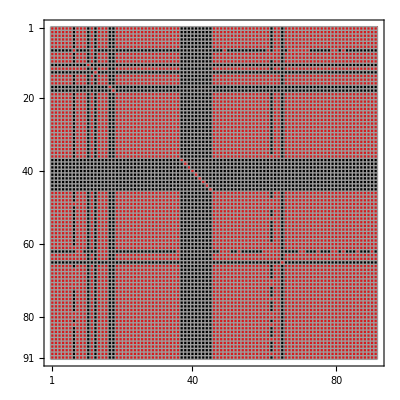

```mathematica
fig=ArrayPlot[Partition[data,Length[models[taskType]]],ColorFunction->cf,Frame->True,Mesh->True,ImageSize->Scaled[0.5],FrameTicksStyle->Opacity[1],FrameTicks->All,ImageMargins->0,
PlotTheme->"Grid",
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->32}
]
```

```mathematica
baseDir=FileNameJoin[{NotebookDirectory[],"figs"}];
Quiet[CreateDirectory[baseDir]];
Export[FileNameJoin[{baseDir,"across_model_flop_sharing.pdf"}], fig,ImageSize->Scaled[1.2],ImageResolution->300]
```

/Users/abduld/papers/synthetic_benchmark_code/figs/across_model_flop_sharing.pdf

## Model Cache

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

## Generate Models MX File

```mathematica
Exit
```

```mathematica
PrependTo[$Path,NotebookDirectory[]];
```

```mathematica
<<SyntheticBenchmark`
<<SyntheticBenchmark`Assets`Models`
```

```mathematica
DumpSaveModelWeights[]
```

## Possible Names

Possible Names:
- PerSe
- Sybe
- ABUDL (* Analytic Benchmarking for Understanding DL *)
- DLSynBench
- SythBench
- Syn

## Scratch

### connected components

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
$ModelNames[[30]]
```

Deep Speech 2 Trained on Baidu English Data

```mathematica
model=NetModel[$ModelNames[[30]]];
```

```mathematica
NetInformation[model,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
NetInformation[model,"SummaryGraphic"]
```

-Graphics-

```mathematica
components=Select[
NetExtract[model,All],
MatchQ[#,_NetGraph]&
]
```

{}

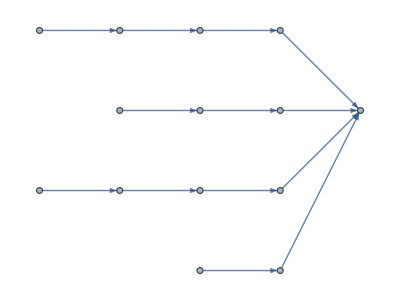

```mathematica
NetInformation[components[[1]],"LayersGraph"]
```

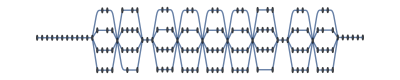

```mathematica
gr0=NetInformation[model,"LayersGraph"];
gr=Graph[VertexList[gr0],EdgeList[gr0]/.DirectedEdge->UndirectedEdge,Options[gr0]]
```

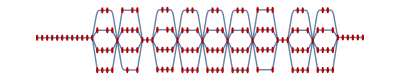

```mathematica
HighlightGraph[gr,ConnectedComponents[gr]]
```

### sequence

```mathematica
ClearAll[timeOf];
timeOf[{a->b,_}]:=ab;
timeOf[{b->c,_}]:=bc;
timeOf[{b->e,e->x_}]:=timeOf[{b->x,dummy}];
timeOf[{e->x_,_}]:=0;
timeOf[{c->d,_}]:=cd;
timeOf[{b->d,_}]:=bd;
```

```mathematica
ClearAll[transform];
transform[b->x_]:=If[RandomInteger[5]>2,{b->e,e->x},b->x];
transform[x_]:=x;
```

```mathematica
net0={a->b,b->c,c->d};
net1={a->b,b->d,c->d};
net2={a->b,b->d};
```

```mathematica
publicNet=Flatten[Map[transform,{net0,net1,net2},{2}]]
```

{a→b,b→c,c→d,a→b,b→e,e→d,c→d,a→b,b→e,e→d}

```mathematica
publicNet=Partition[Append[publicNet,dummy],2,1];
```

```mathematica
publicTimes=Association[Table[First[k]->timeOf[k],{k,publicNet}]]
```

<|(a→b)→ab,(b→c)→bc,(c→d)→cd,(b→e)→bd,(e→d)→0|>

```mathematica
Lookup[publicTimes,net0]
```

{ab,bc,cd}

```mathematica
Lookup[publicTimes,net1]
```

{ab,Missing[KeyAbsent,b→d],cd}

### Benchmarking

```mathematica
<<NeuralNetworks`
```

```mathematica
PrependTo[$ContextPath,"NeuralNetworks`Private`Benchmarking`"];
```

```mathematica
synthesizeData=NeuralNetworks`Private`Benchmarking`synthesizeData;
Inputs=NeuralNetworks`Private`Inputs;
NetAttachLoss=NeuralNetworks`NetAttachLoss;
```

```mathematica
batches=1;
batchSize=1;
NeuralNetworks`Private`Benchmarking`dataSize=batches*batchSize;
sequenceLength=32;
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
modelName="VGG-16 Trained on ImageNet Competition Data";
```

```mathematica
model=NetModel[modelName];
lyrs=NetInformation[model,"Layers"];
```

```mathematica
min=1;
max=11;
lyr=lyrs[[min]];
net=NetChain[Values[lyrs][[min;;max]]];
tnet=NetInitialize@NetAttachLoss[net,Automatic];
SeedRandom[1];
tdata=synthesizeData/@Inputs[lyr];
Min[Table[First[AbsoluteTiming[net[tdata];]],100]]
```

0.153712

```mathematica
net
```

NetChain[<>]

```mathematica
timings=Association@Table[
max=min;
lyr=lyrs[[min]];
name=Keys[lyrs][[min]];
net=NetChain[Values[lyrs][[min;;max]]];
SeedRandom[1];
tdata=synthesizeData/@Inputs[lyr];
name->Mean[Table[First[AbsoluteTiming[net[tdata];]],20]],
{min,Length[lyrs]}
]
```

$Aborted

### A path

```mathematica
benchmarkPath[min_,max_]:=
Module[{},
If[min>max,
0,
lyr=lyrs[[min]];
net=NetChain[Values[lyrs][[min;;max]]];
tnet=NetInitialize@NetAttachLoss[net,Automatic];
SeedRandom[1];
tdata=synthesizeData/@Inputs[lyr];
Mean[Table[First[AbsoluteTiming[net[tdata];]],30]]
]
];
```

```mathematica
Table[
benchmarkPath[ii,ii+1],
{ii,Length[lyrs]-1}
]-Table[
benchmarkPath[ii,ii],
{ii,Length[lyrs]-1}
]
```

{-0.00475973,0.0742654,0.0052875,-0.0232768,0.0422005,0.0206236,0.129338,-0.000930133,-0.00470103,0.0374097,0.0075593,0.0900716,0.0182757,0.054991,0.0140933,0.0138691,0.0323852,0.00695447,0.0551379,0.0110301,0.0356997,0.00137007,0.00186923,0.0202467,-0.00108273,0.0165782,0.00161457,0.0214904,0.0108041,0.00601317,0.00120863,0.0621597,0.0190077,0.000986067,0.0202842,0.002875,0.00106583,0.0021352,0.000468467}

```mathematica
e=Table[
benchmarkPath[ii,ii+1],
{ii,Length[lyrs]-1}
]-Table[
benchmarkPath[ii,ii],
{ii,2,Length[lyrs]}
]
```

```mathematica
{0.012798433333333324,0.06200740000000006,0.13740676666666668,0.011123466666666675,0.030305666666666675,0.051982066666666674,0.03454299999999999,0.0995693333333333,-0.0015040000000000053,0.008412599999999992,0.01910476666666667,-0.006381633333333338,0.04721356666666668,-0.031402799999999995,0.061384699999999986,-0.005882666666666674,0.013778333333333337,0.014691433333333328,-0.03848029999999999,0.044997599999999985,-0.04065659999999999,0.02432986666666666,-0.01901746666666666,-0.015470833333333333,0.00287603333333334,-0.021729866666666667,0.0011149000000000003,-0.010968266666666665,0.0074510c66666666667`,-0.011417699999999996,-0.000928266666666666,-0.08918263333333334,0.04295149999999999,-0.0009643333333333335,-0.012181700000000005,-0.00010793333333333158,-0.0008302000000000003,-0.005439666666666666,-0.00016123333333333337}
```

```mathematica
Total[e]
```

0.415334

```mathematica
benchmarkPath[1,Length[lyrs]]
```

0.483199

### All permutations

```mathematica
tbl=Association@Table[
min=minmax[[1]];
max=minmax[[2]];
minmax->If[min>max,
0,
lyr=lyrs[[min]];
net=NetChain[Values[lyrs][[min;;max]]];
tnet=NetInitialize@NetAttachLoss[net,Automatic];
SeedRandom[1];
tdata=synthesizeData/@Inputs[lyr];
Min[Table[First[AbsoluteTiming[net[tdata];]],10]]
],
{minmax,Tuples[Range[Length[lyrs]],2]}
];
```

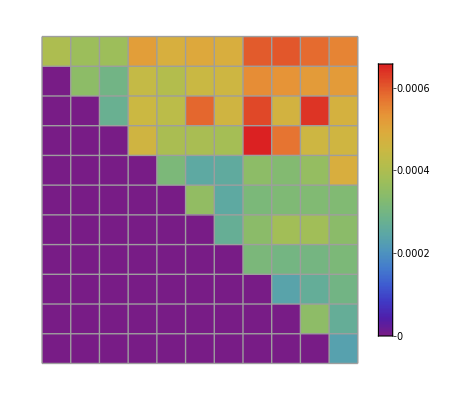

```mathematica
ArrayPlot[
Table[
tbl[{ii,jj}],
{ii,Length[lyrs]},
{jj,Length[lyrs]}
],
ColorFunction->"Rainbow",Mesh->True,PlotLegends->Automatic,ImageSize->Scaled[0.5]
]
```

```mathematica
Table[
tbl[{ii,ii+1}]-tbl[{ii,ii}],
{ii,Length[lyrs]-1}
]
```

{-0.000028,-0.000051,0.000176,-0.000068,-0.000064,-0.000102,0.000073,-0.000013,0.000028,-0.00008}

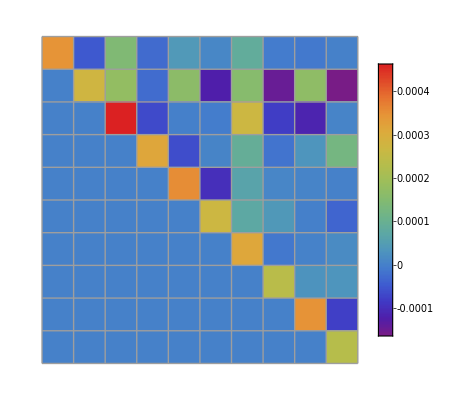

```mathematica
ArrayPlot[Table[
tbl[{ii,jj}]-tbl[{ii,jj-1}],
{ii,2,Length[lyrs]},
{jj,2,Length[lyrs]}
],
ColorFunction->"Rainbow",Mesh->True,PlotLegends->Automatic,ImageSize->Scaled[0.5]]
```

### Export

```mathematica
paramsOf[lyrs[[10]]]
```

<|Type→Elementwise,Arrays→<||>,Parameters→<|Function→ValidatedParameter[Ramp],$Dimensions→{64,56,56}|>,Inputs→<|Input→TensorT[{64,56,56},RealT]|>,Outputs→<|Output→TensorT[{64,56,56},RealT]|>|>

```mathematica
inputDims[lyrs[[16]]]
```

{256,56,56}

```mathematica
paramsOf[lyr_[params_,___]]:=params
```

```mathematica
kernelSize[lyr_[params_,___]]:=With[{e=params["Parameters"]["KernelSize"]},If[ListQ[e],e,""]]
stride[lyr_[params_,___]]:=With[{e=params["Parameters"]["Stride"]},If[ListQ[e],e,""]]
function[lyr_[params_,___]]:=With[{e=params["Parameters"]["Function"]},If[!MissingQ[e],e/.ValidatedParameter->Identity,""]]
dilation[lyr_[params_,___]]:=With[{e=params["Parameters"]["Dilation"]},If[ListQ[e],e,""]]
inputDims[lyr_[params_,___]]:=With[{e=params["Inputs"]},If[AssociationQ[e],If[KeyExistsQ[e,"Input"],e["Input"],e["1"]]/.TensorT[x_,_]:>x,""]]
outputDims[lyr_[params_,___]]:=With[{e=params["Outputs"]},If[AssociationQ[e],e["Output"]/.TensorT[x_,_]:>x,""]]
```

```mathematica
header={"index","kind","layer_name","timing","add","div","comp","exp","mad","input","output","function","kernel","stride","dilation"};
idx=0;
tbl=Table[{
idx++,
StringTrim[SymbolName[Head[lyrs[k]]],"Layer"],
StringRiffle[k,"/"],
timings[k],
Sequence@@Sort[FlopCount[lyrs[k]]],
inputDims[lyrs[k]],
outputDims[lyrs[k]],
function[lyrs[k]],
kernelSize[lyrs[k]],
stride[lyrs[k]],
dilation[lyrs[k]]
},
{k,Keys[timings]}
];
PrependTo[tbl,header];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"data","resnet50.csv"}],tbl]
```

/Users/chengli/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/synthetic_benchmark/data/resnet50.csv

```mathematica
Grid[tbl,
Frame->All,
Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}]
```

index | kind | layer_name | timing | add | div | comp | exp | mad | input | output | function | kernel | stride | dilation
0 | Convolution | conv1 | 0.00914855 | 0 | 0 | 0 | 0 | 118013952 | {3,224,224} | {64,112,112} |  | {7,7} | {2,2} | {1,1}
1 | BatchNormalization | bn_conv1 | 0.0070452 | 0 | 0 | 0 | 802816 | 802816 | {64,112,112} | {64,112,112} |  |  |  | 
2 | Elementwise | conv1_relu | 0.0064848 | 0 | 0 | 0 | 802816 | 802816 | {64,112,112} | {64,112,112} | Ramp |  |  | 
3 | Padding | pool1_pad | 0.00545615 | 0 | 0 | 0 | 0 | 0 | {64,112,112} | {64,113,113} |  |  |  | 
4 | Pooling | pool1 | 0.0084406 | 0 | 0 | 0 | 0 | 1806336 | {64,113,113} | {64,56,56} | Max | {3,3} | {2,2} | 
5 | Convolution | 2a/res2a_branch1 | 0.0053301 | 0 | 0 | 0 | 0 | 51380224 | {64,56,56} | {256,56,56} |  | {1,1} | {1,1} | {1,1}
6 | BatchNormalization | 2a/bn2a_branch1 | 0.00769585 | 0 | 0 | 0 | 802816 | 802816 | {256,56,56} | {256,56,56} |  |  |  | 
7 | Convolution | 2a/res2a_branch2a | 0.00587515 | 0 | 0 | 0 | 0 | 12845056 | {64,56,56} | {64,56,56} |  | {1,1} | {1,1} | {1,1}
8 | BatchNormalization | 2a/bn2a_branch2a | 0.00513625 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} |  |  |  | 
9 | Elementwise | 2a/res2a_branch2a_relu | 0.00254355 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} | Ramp |  |  | 
10 | Convolution | 2a/res2a_branch2b | 0.00775925 | 0 | 0 | 0 | 0 | 115605504 | {64,56,56} | {64,56,56} |  | {3,3} | {1,1} | {1,1}
11 | BatchNormalization | 2a/bn2a_branch2b | 0.0022689 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} |  |  |  | 
12 | Elementwise | 2a/res2a_branch2b_relu | 0.0019194 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} | Ramp |  |  | 
13 | Convolution | 2a/res2a_branch2c | 0.0051266 | 0 | 0 | 0 | 0 | 51380224 | {64,56,56} | {256,56,56} |  | {1,1} | {1,1} | {1,1}
14 | BatchNormalization | 2a/bn2a_branch2c | 0.00506775 | 0 | 0 | 0 | 802816 | 802816 | {256,56,56} | {256,56,56} |  |  |  | 
15 | Total | 2a/res2a | 0.00621945 | 0 | 0 | 0 | 0 | 802816 | {256,56,56} | {256,56,56} |  |  |  | 
16 | Elementwise | 2a/res2a_relu | 0.0054392 | 0 | 0 | 0 | 802816 | 802816 | {256,56,56} | {256,56,56} | Ramp |  |  | 
17 | Convolution | 2b/res2b_branch2a | 0.00758225 | 0 | 0 | 0 | 0 | 51380224 | {256,56,56} | {64,56,56} |  | {1,1} | {1,1} | {1,1}
18 | BatchNormalization | 2b/bn2b_branch2a | 0.0045345 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} |  |  |  | 
19 | Elementwise | 2b/res2b_branch2a_relu | 0.00402545 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} | Ramp |  |  | 
20 | Convolution | 2b/res2b_branch2b | 0.0053188 | 0 | 0 | 0 | 0 | 115605504 | {64,56,56} | {64,56,56} |  | {3,3} | {1,1} | {1,1}
21 | BatchNormalization | 2b/bn2b_branch2b | 0.00186745 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} |  |  |  | 
22 | Elementwise | 2b/res2b_branch2b_relu | 0.00193465 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} | Ramp |  |  | 
23 | Convolution | 2b/res2b_branch2c | 0.00581255 | 0 | 0 | 0 | 0 | 51380224 | {64,56,56} | {256,56,56} |  | {1,1} | {1,1} | {1,1}
24 | BatchNormalization | 2b/bn2b_branch2c | 0.00454885 | 0 | 0 | 0 | 802816 | 802816 | {256,56,56} | {256,56,56} |  |  |  | 
25 | Total | 2b/res2b | 0.00524855 | 0 | 0 | 0 | 0 | 802816 | {256,56,56} | {256,56,56} |  |  |  | 
26 | Elementwise | 2b/res2b_relu | 0.00494205 | 0 | 0 | 0 | 802816 | 802816 | {256,56,56} | {256,56,56} | Ramp |  |  | 
27 | Convolution | 2c/res2c_branch2a | 0.007397 | 0 | 0 | 0 | 0 | 51380224 | {256,56,56} | {64,56,56} |  | {1,1} | {1,1} | {1,1}
28 | BatchNormalization | 2c/bn2c_branch2a | 0.0049177 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} |  |  |  | 
29 | Elementwise | 2c/res2c_branch2a_relu | 0.00372945 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} | Ramp |  |  | 
30 | Convolution | 2c/res2c_branch2b | 0.00484165 | 0 | 0 | 0 | 0 | 115605504 | {64,56,56} | {64,56,56} |  | {3,3} | {1,1} | {1,1}
31 | BatchNormalization | 2c/bn2c_branch2b | 0.00187095 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} |  |  |  | 
32 | Elementwise | 2c/res2c_branch2b_relu | 0.00182295 | 0 | 0 | 0 | 200704 | 200704 | {64,56,56} | {64,56,56} | Ramp |  |  | 
33 | Convolution | 2c/res2c_branch2c | 0.00547275 | 0 | 0 | 0 | 0 | 51380224 | {64,56,56} | {256,56,56} |  | {1,1} | {1,1} | {1,1}
34 | BatchNormalization | 2c/bn2c_branch2c | 0.0049768 | 0 | 0 | 0 | 802816 | 802816 | {256,56,56} | {256,56,56} |  |  |  | 
35 | Total | 2c/res2c | 0.006243 | 0 | 0 | 0 | 0 | 802816 | {256,56,56} | {256,56,56} |  |  |  | 
36 | Elementwise | 2c/res2c_relu | 0.00524415 | 0 | 0 | 0 | 802816 | 802816 | {256,56,56} | {256,56,56} | Ramp |  |  | 
37 | Convolution | 3a/res3a_branch1 | 0.00860335 | 0 | 0 | 0 | 0 | 102760448 | {256,56,56} | {512,28,28} |  | {1,1} | {2,2} | {1,1}
38 | BatchNormalization | 3a/bn3a_branch1 | 0.0034124 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
39 | Convolution | 3a/res3a_branch2a | 0.0072233 | 0 | 0 | 0 | 0 | 25690112 | {256,56,56} | {128,28,28} |  | {1,1} | {2,2} | {1,1}
40 | BatchNormalization | 3a/bn3a_branch2a | 0.0036107 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
41 | Elementwise | 3a/res3a_branch2a_relu | 0.0039455 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
42 | Convolution | 3a/res3a_branch2b | 0.0043155 | 0 | 0 | 0 | 0 | 115605504 | {128,28,28} | {128,28,28} |  | {3,3} | {1,1} | {1,1}
43 | BatchNormalization | 3a/bn3a_branch2b | 0.00153465 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
44 | Elementwise | 3a/res3a_branch2b_relu | 0.00143795 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
45 | Convolution | 3a/res3a_branch2c | 0.00327575 | 0 | 0 | 0 | 0 | 51380224 | {128,28,28} | {512,28,28} |  | {1,1} | {1,1} | {1,1}
46 | BatchNormalization | 3a/bn3a_branch2c | 0.0041595 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
47 | Total | 3a/res3a | 0.0039876 | 0 | 0 | 0 | 0 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
48 | Elementwise | 3a/res3a_relu | 0.00305575 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} | Ramp |  |  | 
49 | Convolution | 3b/res3b_branch2a | 0.00619455 | 0 | 0 | 0 | 0 | 51380224 | {512,28,28} | {128,28,28} |  | {1,1} | {1,1} | {1,1}
50 | BatchNormalization | 3b/bn3b_branch2a | 0.00405845 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
51 | Elementwise | 3b/res3b_branch2a_relu | 0.00335545 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
52 | Convolution | 3b/res3b_branch2b | 0.00378615 | 0 | 0 | 0 | 0 | 115605504 | {128,28,28} | {128,28,28} |  | {3,3} | {1,1} | {1,1}
53 | BatchNormalization | 3b/bn3b_branch2b | 0.00168205 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
54 | Elementwise | 3b/res3b_branch2b_relu | 0.0015809 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
55 | Convolution | 3b/res3b_branch2c | 0.0035219 | 0 | 0 | 0 | 0 | 51380224 | {128,28,28} | {512,28,28} |  | {1,1} | {1,1} | {1,1}
56 | BatchNormalization | 3b/bn3b_branch2c | 0.0048676 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
57 | Total | 3b/res3b | 0.00431565 | 0 | 0 | 0 | 0 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
58 | Elementwise | 3b/res3b_relu | 0.00294855 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} | Ramp |  |  | 
59 | Convolution | 3c/res3c_branch2a | 0.00647215 | 0 | 0 | 0 | 0 | 51380224 | {512,28,28} | {128,28,28} |  | {1,1} | {1,1} | {1,1}
60 | BatchNormalization | 3c/bn3c_branch2a | 0.0040417 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
61 | Elementwise | 3c/res3c_branch2a_relu | 0.0033902 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
62 | Convolution | 3c/res3c_branch2b | 0.0036709 | 0 | 0 | 0 | 0 | 115605504 | {128,28,28} | {128,28,28} |  | {3,3} | {1,1} | {1,1}
63 | BatchNormalization | 3c/bn3c_branch2b | 0.00155785 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
64 | Elementwise | 3c/res3c_branch2b_relu | 0.0014171 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
65 | Convolution | 3c/res3c_branch2c | 0.00354615 | 0 | 0 | 0 | 0 | 51380224 | {128,28,28} | {512,28,28} |  | {1,1} | {1,1} | {1,1}
66 | BatchNormalization | 3c/bn3c_branch2c | 0.00286265 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
67 | Total | 3c/res3c | 0.0042794 | 0 | 0 | 0 | 0 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
68 | Elementwise | 3c/res3c_relu | 0.0024139 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} | Ramp |  |  | 
69 | Convolution | 3d/res3d_branch2a | 0.00618495 | 0 | 0 | 0 | 0 | 51380224 | {512,28,28} | {128,28,28} |  | {1,1} | {1,1} | {1,1}
70 | BatchNormalization | 3d/bn3d_branch2a | 0.0040246 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
71 | Elementwise | 3d/res3d_branch2a_relu | 0.0032989 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
72 | Convolution | 3d/res3d_branch2b | 0.003783 | 0 | 0 | 0 | 0 | 115605504 | {128,28,28} | {128,28,28} |  | {3,3} | {1,1} | {1,1}
73 | BatchNormalization | 3d/bn3d_branch2b | 0.0016608 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} |  |  |  | 
74 | Elementwise | 3d/res3d_branch2b_relu | 0.00160445 | 0 | 0 | 0 | 100352 | 100352 | {128,28,28} | {128,28,28} | Ramp |  |  | 
75 | Convolution | 3d/res3d_branch2c | 0.00323875 | 0 | 0 | 0 | 0 | 51380224 | {128,28,28} | {512,28,28} |  | {1,1} | {1,1} | {1,1}
76 | BatchNormalization | 3d/bn3d_branch2c | 0.0044167 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
77 | Total | 3d/res3d | 0.00395835 | 0 | 0 | 0 | 0 | 401408 | {512,28,28} | {512,28,28} |  |  |  | 
78 | Elementwise | 3d/res3d_relu | 0.00264315 | 0 | 0 | 0 | 401408 | 401408 | {512,28,28} | {512,28,28} | Ramp |  |  | 
79 | Convolution | 4a/res4a_branch1 | 0.00647305 | 0 | 0 | 0 | 0 | 102760448 | {512,28,28} | {1024,14,14} |  | {1,1} | {2,2} | {1,1}
80 | BatchNormalization | 4a/bn4a_branch1 | 0.00272165 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
81 | Convolution | 4a/res4a_branch2a | 0.0065323 | 0 | 0 | 0 | 0 | 25690112 | {512,28,28} | {256,14,14} |  | {1,1} | {2,2} | {1,1}
82 | BatchNormalization | 4a/bn4a_branch2a | 0.00357535 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
83 | Elementwise | 4a/res4a_branch2a_relu | 0.0035066 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
84 | Convolution | 4a/res4a_branch2b | 0.00324325 | 0 | 0 | 0 | 0 | 115605504 | {256,14,14} | {256,14,14} |  | {3,3} | {1,1} | {1,1}
85 | BatchNormalization | 4a/bn4a_branch2b | 0.0014168 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
86 | Elementwise | 4a/res4a_branch2b_relu | 0.0014899 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
87 | Convolution | 4a/res4a_branch2c | 0.00329125 | 0 | 0 | 0 | 0 | 51380224 | {256,14,14} | {1024,14,14} |  | {1,1} | {1,1} | {1,1}
88 | BatchNormalization | 4a/bn4a_branch2c | 0.00417085 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
89 | Total | 4a/res4a | 0.003678 | 0 | 0 | 0 | 0 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
90 | Elementwise | 4a/res4a_relu | 0.0024805 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} | Ramp |  |  | 
91 | Convolution | 4b/res4b_branch2a | 0.0058556 | 0 | 0 | 0 | 0 | 51380224 | {1024,14,14} | {256,14,14} |  | {1,1} | {1,1} | {1,1}
92 | BatchNormalization | 4b/bn4b_branch2a | 0.0020001 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
93 | Elementwise | 4b/res4b_branch2a_relu | 0.0037084 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
94 | Convolution | 4b/res4b_branch2b | 0.0034178 | 0 | 0 | 0 | 0 | 115605504 | {256,14,14} | {256,14,14} |  | {3,3} | {1,1} | {1,1}
95 | BatchNormalization | 4b/bn4b_branch2b | 0.00138815 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
96 | Elementwise | 4b/res4b_branch2b_relu | 0.00134225 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
97 | Convolution | 4b/res4b_branch2c | 0.0028691 | 0 | 0 | 0 | 0 | 51380224 | {256,14,14} | {1024,14,14} |  | {1,1} | {1,1} | {1,1}
98 | BatchNormalization | 4b/bn4b_branch2c | 0.00416345 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
99 | Total | 4b/res4b | 0.00376475 | 0 | 0 | 0 | 0 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
100 | Elementwise | 4b/res4b_relu | 0.00286505 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} | Ramp |  |  | 
101 | Convolution | 4c/res4c_branch2a | 0.0058474 | 0 | 0 | 0 | 0 | 51380224 | {1024,14,14} | {256,14,14} |  | {1,1} | {1,1} | {1,1}
102 | BatchNormalization | 4c/bn4c_branch2a | 0.00184755 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
103 | Elementwise | 4c/res4c_branch2a_relu | 0.00323325 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
104 | Convolution | 4c/res4c_branch2b | 0.0033043 | 0 | 0 | 0 | 0 | 115605504 | {256,14,14} | {256,14,14} |  | {3,3} | {1,1} | {1,1}
105 | BatchNormalization | 4c/bn4c_branch2b | 0.00139125 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
106 | Elementwise | 4c/res4c_branch2b_relu | 0.0012937 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
107 | Convolution | 4c/res4c_branch2c | 0.0033545 | 0 | 0 | 0 | 0 | 51380224 | {256,14,14} | {1024,14,14} |  | {1,1} | {1,1} | {1,1}
108 | BatchNormalization | 4c/bn4c_branch2c | 0.00437505 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
109 | Total | 4c/res4c | 0.00368275 | 0 | 0 | 0 | 0 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
110 | Elementwise | 4c/res4c_relu | 0.00252505 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} | Ramp |  |  | 
111 | Convolution | 4d/res4d_branch2a | 0.00591415 | 0 | 0 | 0 | 0 | 51380224 | {1024,14,14} | {256,14,14} |  | {1,1} | {1,1} | {1,1}
112 | BatchNormalization | 4d/bn4d_branch2a | 0.0041214 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
113 | Elementwise | 4d/res4d_branch2a_relu | 0.00370585 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
114 | Convolution | 4d/res4d_branch2b | 0.00418585 | 0 | 0 | 0 | 0 | 115605504 | {256,14,14} | {256,14,14} |  | {3,3} | {1,1} | {1,1}
115 | BatchNormalization | 4d/bn4d_branch2b | 0.00138715 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
116 | Elementwise | 4d/res4d_branch2b_relu | 0.00126665 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
117 | Convolution | 4d/res4d_branch2c | 0.00279045 | 0 | 0 | 0 | 0 | 51380224 | {256,14,14} | {1024,14,14} |  | {1,1} | {1,1} | {1,1}
118 | BatchNormalization | 4d/bn4d_branch2c | 0.0042417 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
119 | Total | 4d/res4d | 0.0034411 | 0 | 0 | 0 | 0 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
120 | Elementwise | 4d/res4d_relu | 0.00275765 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} | Ramp |  |  | 
121 | Convolution | 4e/res4e_branch2a | 0.00602715 | 0 | 0 | 0 | 0 | 51380224 | {1024,14,14} | {256,14,14} |  | {1,1} | {1,1} | {1,1}
122 | BatchNormalization | 4e/bn4e_branch2a | 0.00194765 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
123 | Elementwise | 4e/res4e_branch2a_relu | 0.0034867 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
124 | Convolution | 4e/res4e_branch2b | 0.00359035 | 0 | 0 | 0 | 0 | 115605504 | {256,14,14} | {256,14,14} |  | {3,3} | {1,1} | {1,1}
125 | BatchNormalization | 4e/bn4e_branch2b | 0.00134635 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
126 | Elementwise | 4e/res4e_branch2b_relu | 0.0012731 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
127 | Convolution | 4e/res4e_branch2c | 0.00325975 | 0 | 0 | 0 | 0 | 51380224 | {256,14,14} | {1024,14,14} |  | {1,1} | {1,1} | {1,1}
128 | BatchNormalization | 4e/bn4e_branch2c | 0.00465435 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
129 | Total | 4e/res4e | 0.0034135 | 0 | 0 | 0 | 0 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
130 | Elementwise | 4e/res4e_relu | 0.0024535 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} | Ramp |  |  | 
131 | Convolution | 4f/res4f_branch2a | 0.00582495 | 0 | 0 | 0 | 0 | 51380224 | {1024,14,14} | {256,14,14} |  | {1,1} | {1,1} | {1,1}
132 | BatchNormalization | 4f/bn4f_branch2a | 0.0018157 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
133 | Elementwise | 4f/res4f_branch2a_relu | 0.0033267 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
134 | Convolution | 4f/res4f_branch2b | 0.00403065 | 0 | 0 | 0 | 0 | 115605504 | {256,14,14} | {256,14,14} |  | {3,3} | {1,1} | {1,1}
135 | BatchNormalization | 4f/bn4f_branch2b | 0.00143735 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} |  |  |  | 
136 | Elementwise | 4f/res4f_branch2b_relu | 0.00133195 | 0 | 0 | 0 | 50176 | 50176 | {256,14,14} | {256,14,14} | Ramp |  |  | 
137 | Convolution | 4f/res4f_branch2c | 0.00281415 | 0 | 0 | 0 | 0 | 51380224 | {256,14,14} | {1024,14,14} |  | {1,1} | {1,1} | {1,1}
138 | BatchNormalization | 4f/bn4f_branch2c | 0.0041527 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
139 | Total | 4f/res4f | 0.0035611 | 0 | 0 | 0 | 0 | 200704 | {1024,14,14} | {1024,14,14} |  |  |  | 
140 | Elementwise | 4f/res4f_relu | 0.0025297 | 0 | 0 | 0 | 200704 | 200704 | {1024,14,14} | {1024,14,14} | Ramp |  |  | 
141 | Convolution | 5a/res5a_branch1 | 0.00777915 | 0 | 0 | 0 | 0 | 102760448 | {1024,14,14} | {2048,7,7} |  | {1,1} | {2,2} | {1,1}
142 | BatchNormalization | 5a/bn5a_branch1 | 0.00212325 | 0 | 0 | 0 | 100352 | 100352 | {2048,7,7} | {2048,7,7} |  |  |  | 
143 | Convolution | 5a/res5a_branch2a | 0.00637825 | 0 | 0 | 0 | 0 | 25690112 | {1024,14,14} | {512,7,7} |  | {1,1} | {2,2} | {1,1}
144 | BatchNormalization | 5a/bn5a_branch2a | 0.00269085 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} |  |  |  | 
145 | Elementwise | 5a/res5a_branch2a_relu | 0.00191845 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} | Ramp |  |  | 
146 | Convolution | 5a/res5a_branch2b | 0.00312585 | 0 | 0 | 0 | 0 | 115605504 | {512,7,7} | {512,7,7} |  | {3,3} | {1,1} | {1,1}
147 | BatchNormalization | 5a/bn5a_branch2b | 0.0011571 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} |  |  |  | 
148 | Elementwise | 5a/res5a_branch2b_relu | 0.0010594 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} | Ramp |  |  | 
149 | Convolution | 5a/res5a_branch2c | 0.0026057 | 0 | 0 | 0 | 0 | 51380224 | {512,7,7} | {2048,7,7} |  | {1,1} | {1,1} | {1,1}
150 | BatchNormalization | 5a/bn5a_branch2c | 0.0037363 | 0 | 0 | 0 | 100352 | 100352 | {2048,7,7} | {2048,7,7} |  |  |  | 
151 | Total | 5a/res5a | 0.0030358 | 0 | 0 | 0 | 0 | 100352 | {2048,7,7} | {2048,7,7} |  |  |  | 
152 | Elementwise | 5a/res5a_relu | 0.00210015 | 0 | 0 | 0 | 100352 | 100352 | {2048,7,7} | {2048,7,7} | Ramp |  |  | 
153 | Convolution | 5b/res5b_branch2a | 0.00505085 | 0 | 0 | 0 | 0 | 51380224 | {2048,7,7} | {512,7,7} |  | {1,1} | {1,1} | {1,1}
154 | BatchNormalization | 5b/bn5b_branch2a | 0.0020409 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} |  |  |  | 
155 | Elementwise | 5b/res5b_branch2a_relu | 0.00202135 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} | Ramp |  |  | 
156 | Convolution | 5b/res5b_branch2b | 0.00492525 | 0 | 0 | 0 | 0 | 115605504 | {512,7,7} | {512,7,7} |  | {3,3} | {1,1} | {1,1}
157 | BatchNormalization | 5b/bn5b_branch2b | 0.0011748 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} |  |  |  | 
158 | Elementwise | 5b/res5b_branch2b_relu | 0.00091965 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} | Ramp |  |  | 
159 | Convolution | 5b/res5b_branch2c | 0.00211365 | 0 | 0 | 0 | 0 | 51380224 | {512,7,7} | {2048,7,7} |  | {1,1} | {1,1} | {1,1}
160 | BatchNormalization | 5b/bn5b_branch2c | 0.00335375 | 0 | 0 | 0 | 100352 | 100352 | {2048,7,7} | {2048,7,7} |  |  |  | 
161 | Total | 5b/res5b | 0.003155 | 0 | 0 | 0 | 0 | 100352 | {2048,7,7} | {2048,7,7} |  |  |  | 
162 | Elementwise | 5b/res5b_relu | 0.00216615 | 0 | 0 | 0 | 100352 | 100352 | {2048,7,7} | {2048,7,7} | Ramp |  |  | 
163 | Convolution | 5c/res5c_branch2a | 0.004968 | 0 | 0 | 0 | 0 | 51380224 | {2048,7,7} | {512,7,7} |  | {1,1} | {1,1} | {1,1}
164 | BatchNormalization | 5c/bn5c_branch2a | 0.00225925 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} |  |  |  | 
165 | Elementwise | 5c/res5c_branch2a_relu | 0.00218695 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} | Ramp |  |  | 
166 | Convolution | 5c/res5c_branch2b | 0.0037493 | 0 | 0 | 0 | 0 | 115605504 | {512,7,7} | {512,7,7} |  | {3,3} | {1,1} | {1,1}
167 | BatchNormalization | 5c/bn5c_branch2b | 0.0010563 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} |  |  |  | 
168 | Elementwise | 5c/res5c_branch2b_relu | 0.0008819 | 0 | 0 | 0 | 25088 | 25088 | {512,7,7} | {512,7,7} | Ramp |  |  | 
169 | Convolution | 5c/res5c_branch2c | 0.00244945 | 0 | 0 | 0 | 0 | 51380224 | {512,7,7} | {2048,7,7} |  | {1,1} | {1,1} | {1,1}
170 | BatchNormalization | 5c/bn5c_branch2c | 0.0035349 | 0 | 0 | 0 | 100352 | 100352 | {2048,7,7} | {2048,7,7} |  |  |  | 
171 | Total | 5c/res5c | 0.003021 | 0 | 0 | 0 | 0 | 100352 | {2048,7,7} | {2048,7,7} |  |  |  | 
172 | Elementwise | 5c/res5c_relu | 0.0022482 | 0 | 0 | 0 | 100352 | 100352 | {2048,7,7} | {2048,7,7} | Ramp |  |  | 
173 | Pooling | pool5 | 0.0062615 | 0 | 0 | 0 | 0 | 100352 | {2048,7,7} | {2048,1,1} | Mean | {7,7} | {1,1} | 
174 | Flatten | flatten_0 | 0.0005724 | 0 | 0 | 0 | 0 | 0 | {2048,1,1} | {2048} |  |  |  | 
175 | Linear | fc1000 | 0.00142875 | 0 | 0 | 0 | 0 | 2048000 | {2048} | {1000} |  |  |  | 
176 | Softmax | prob | 0.00059425 | 0 | 0 | 1000 | 1000 | 1000 | {1000} | {1000} |  |  |  |

### Other

```mathematica
NetInformation[lyrs[[2]],"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
NetInformation[model,"SummaryGraphic"]
```

-Graphics-

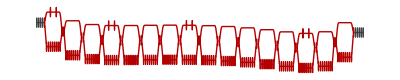

```mathematica
gr=UndirectedGraph[ NetInformation[model,"LayersGraph"]];
cycles=FindCycle[gr,Infinity,All];
Fold[HighlightGraph[#1,PathGraph[#2]]&,gr,cycles]
```

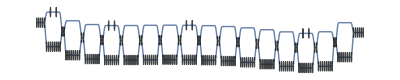

```mathematica
gr
```

```mathematica
NetInformation[lyrs[[2]],"InputPorts"]
```

<|Input→{64,112,112}|>

```mathematica
lyrs[[2]]
```

BatchNormalizationLayer[<>]

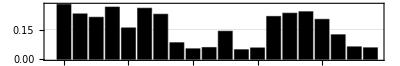

```mathematica
BarChart[
timings,
ChartLabels->Map[Style[#,FontSize->10,FontFamily->"Latin Modern Roman"]&,Keys[timings]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

### Hatching

```mathematica
inPolyQ=Compile[{{polygon,_Real,2},{x,_Real},{y,_Real}},Block[{polySides=Length[polygon],X=polygon[[All,1]],Y=polygon[[All,2]],Xi,Yi,Yip1,wn=0,i=1},While[i<polySides,Yi=Y[[i]];Yip1=Y[[i+1]];
If[Yi≤y,If[Yip1>y,Xi=X[[i]];
If[(X[[i+1]]-Xi) (y-Yi)-(x-Xi) (Yip1-Yi)>0,wn++;];];,If[Yip1≤y,Xi=X[[i]];
If[(X[[i+1]]-Xi) (y-Yi)-(x-Xi) (Yip1-Yi)<0,wn--;];];];i++];!wn==0]];
```

```mathematica
poly=Rescale[ExampleData[{"Statistics","WesternUgandaBorder"}]];
```

CompiledFunction::cfsa: Argument x at position 2 should be a machine-size real number.

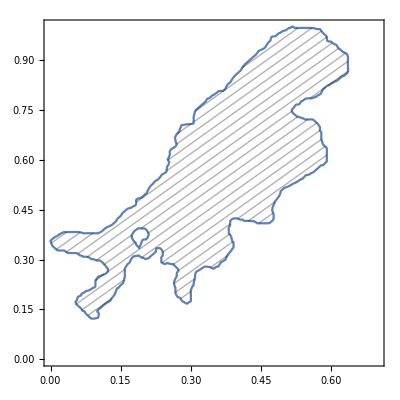

<|2D Face Alignment Net Trained on 300W Large Pose Data→{1},90,YOLO V2 Trained on MS-COCO Data→{ConvolutionLayer[<|Type→Convolution,3,Outputs→<|Output→NeuralNetworks`TensorT[{32,416,416},NeuralNetworks`RealT]|>|>,<|1|>],104,TransposeLayer[1]}|>
 |  |  |  |

```mathematica
RegionPlot[inPolyQ[poly,x,y],{x,0,.7},{y,0,1},Mesh->20,MeshFunctions->{#1-#2&},MeshShading->{None},PlotPoints->25]
```